To get started, evaluate everything through Octopeda: octopus subst functions

Getting Started

#### A minor preliminary

```mathematica
Off[General::"spell1"];
Off[Graphics::"gprim"];
Off[Polygon::"list"];
```

#### Hyperbolic and Spherical Trig

I' m tired of forgetting these equations, so here they are forever :

For hyperbolic triangle with vertices A, B, C and edges a, b, c  we have :
  
  Sinh[b] Sinh[c] Cos[A] === + Cosh[b] Cosh [c] - Cosh [a]

Sin[B] Sin[C] Cosh[a] === + Cos[B] Cos[C] + Cos[A]

Sinh[a]/Sin[A] === Sinh[b]/Sin[B]

For spherical triangle with vertices ABC and edges abc we have

Sin[b] Sin[c] Cos[A] === - Cos[b] Cos[c] + Cos[a]

+ Cos[A] +  Cos[B] Cos[C] ===  Sin[B] Sin[C] Cos[a]
	
Sin[a]/Sin[A] === Sin[b]/Sin[B]

## Defining transforms

### Defining the algebra

Defining our own notation for conjuagacy; this is entered as bu

```mathematica
x_^•:=Conjugate[x]
```

#### getting started

Defining how transforms apply:

```mathematica
SetAttributes[SmallCircle,{Flat,OneIdentity,Listable}]
```

General Mobius Transformations:

```mathematica
Mobius[Mobius[A_]]:=Mobius[A]
```

```mathematica
Mobius[A_]∘Mobius[B_]:=Mobius[B.A]

Mobius[|a_,c_|]:=Mobius[{{a,c^•},{c,a^•}}]
```

```mathematica
inverse[|a_,c_|]:=|Conjugate[a]/(a^2-c^2),-c/(a^2-c^2)|
inverse[Mobius[|a_,c_|]]:=inverse[|a,c|]
inverse[Mobius[{{a_,b_},{c_,d_}}]]:=Mobius[{{d,-b},{-c,a}}/(a d - b c)]
inverse[Mobius[{a_,c_}]]:=inverse[Mobius[|a,c|]]
```

```mathematica
fixedpts[Mobius[{{a_,b_},{c_,d_}}]]:=z/.Solve[(a z + b)==(c z + d)z,z]
```

The code is written presuming that it is good style to always use the Mobius wrapper. This allows us to forget it sometimes. However, similar shortcuts are not implemented for the non-orientation preserving operations. Next time the code is written, this should all be made more transparent.

```mathematica
normalize[Mobius[{{a_,b_},{c_,d_}}]]:=
Mobius[
{{a,b},{c,d}}/Det[{{a,b},{c,d}}]*
Which[
Re[a]!=0,Sign[Re[a]],
Im[a]!=0,Sign[Im[a]],
Re[b]!=0,Sign[Re[b]],
Im[b]!=0,Sign[Im[b]],
Re[c]!=0,Sign[Re[c]],
Im[c]!=0,Sign[Im[c]],
Re[d]!=0,Sign[Re[d]],
Im[d]!=0,Sign[Im[d]],
True, 1(*"ERROR"*)]]
normalize[Conjugate[Mobius[A_]]]:=Conjugate[normalize[Mobius[A]]]
```

```mathematica
|a_,c_|∘|b_,d_|:=Mobius[|a,c|]∘Mobius[|b,d|]

Mobius[A_]∘|b_,d_|:=Mobius[A]∘Mobius[|b,d|]

|a_,c_|∘Mobius[B_]:=Mobius[|a,c|]∘Mobius[B]
```

```mathematica
LinFrac=Compile[{{z,_Complex},{a, _Complex},{b, _Complex},{c, _Complex}, {d, _Complex}},(a z + b)/(c z + d)];
```

Orientation preserving: where Modulus[a]-Modulus[c]=1 (can scale by real)

```mathematica
LinFracOrPr=Compile[{{z,_Complex},{a, _Complex},{c, _Complex}},
		(a z+c^•)/(c z + a^•)];
```

```mathematica
z_∘|a_,c_|:=LinFracOrPr[z,a,c]
```

```mathematica
Clear[power];
power[a_,0]:=|1,0|;
power[a_,1]:=a;
power[a_,n_?((IntegerQ[#]&&#>=2)&)]:=(power[a,(n-1)])∘a;
```

#### Adding the non-orientation preserving algebra

Reflections: where Modulus[a]-Modulus[c]=1

Remember, operations read left to right!

```mathematica
Mobius[Conjugate[Mobius[x_]]]:=Conjugate[Mobius[x]]
```

```mathematica
Mobius[‖a_,c_‖]:=Mobius[{{a,c^•},{c,a^•}}]^•

Mobius[A_]^•∘Mobius[B_]:=Mobius[B.A]^•

Mobius[A_]∘Mobius[B_]^•:=Mobius[B.A^•]^•

Mobius[A_]^•∘Mobius[B_]^•:=Mobius[B.A^•]
```

```mathematica
LinFracOR=Compile[{{z,_Complex},{a, _Complex},{b, _Complex},{c, _Complex}, {d, _Complex}},(a z^• + b)/(c z^• + d)];

LinFracOrRev=Compile[{{z,_Complex},{a, _Complex},{c, _Complex}},
		(a z^•+c^•)/(c z^• + a^•)];

z_∘‖a_,c_‖:=LinFracOrRev[z,a,c]
```

```mathematica
inverse[Conjugate[Mobius[{{a_,b_},{c_,d_}}]]]:=Conjugate[Mobius[{{Conjugate[d],-Conjugate[b]},{-Conjugate[c],Conjugate[a]}}]]

inverse[Conjugate[Mobius[{a_,c_}]]]:=inverse[Mobius[{{a,Conjugate[c]},{c,Conjugate[a]}}]]
```

#### Another def (sans the wrapper)

```mathematica
z_∘Mobius[{{a_,b_},{c_,d_}}]:=LinFrac[z,a,b,c,d]

z_∘Mobius[{{a_,b_},{c_,d_}}]^•=LinFracOR[z,a,b,c,d];
```

CompiledFunction::cfsa: Argument z at position 1 should be a machine-size complex number.

Reflect across the x axis

```mathematica
Refx=‖1,0‖;
Refy= ‖-I,0‖;
```

### Specific operations

```mathematica
Ident:=|1.,0.|
```

Rotate by θ around the origin

```mathematica
Rot[θ_]:=|E^(I/2 θ)//N,0|;
```

Translate along the x-axis

```mathematica
Trans[τ_]:=|Cosh[τ/2]//N,Sinh[τ/2]//N|;
```

Taking Conformal disk to conformal half plane, and back:

```mathematica
Plane2Disk=Mobius[({{I, 1}, {-I, 1}})];
```

```mathematica
Disk2Plane=Mobius[({{-I/2, I/2}, {1/2, 1/2}})];
```

Parabolic elements fixing 1: (in upper half plane model,  z->z+τ)

```mathematica
Parabolic[τ_]:=|τ-2I,τ|
```

Now taking any given point to any other given point along the geodesic through them both:

```mathematica
Trans2Point[v_,w_]:=|w v^•-1,v^•-w^•|;
```

```mathematica
DiskDistance=Compile[{{v,_Complex},{w,_Complex}},
		2ArcTanh[Abs[(w-v)/(1-v^•w)]
			]];
```

```mathematica
DiskAngleBetwixt[a_,b_,c_]:=
	Arg[c∘Mobius[Trans2Point[b,0]]∘Rot[-Arg[a∘Trans2Point[b,0]]]]
```

```mathematica
Trans2Point[v_,0,τ_]:=|Abs[v],Tanh[-τ/2] v^•|;
```

Don't ask where this amusing formula came from.

```mathematica
trans2PointArith=Compile[{{v,_Complex},{w,_Complex},{τ,_Real}},{-Abs[(-v+w ) (-1+v w^•)]+(w v^•-v w^•) Tanh[τ/2],(v^•-w^•-w^•  v v^•+v^• w w^•)Tanh[τ/2]}];
```

```mathematica
Trans2Point[v_,w_,τ_]:=|#1,#2|&@@trans2PointArith[v,w,τ];
```

```mathematica
rotAboutPointArith=Compile[{{v,_Complex},{θ,_Real}},{E^((I θ)/2)-E^(-(I θ)/2) v^• v,v^• (-E^(-(I θ)/2)+E^((I θ)/2))}];
```

```mathematica
RotAboutPt[v_,θ_]:=|#1,#2|&@@rotAboutPointArith[v,θ]
```

#### conversions between models

```mathematica
Poinc2Klein[v_]:=P2KArith[v]
	
	
	P2KArith=Compile[{{v,_Complex}},(2v)/(1+  v v^•)];
```

### Plotting Points and Arcs

```mathematica
movestuff= Transpose@Outer[#1∘#2&,#1,#2]&;

movestuffs=Module[{a=#1,b=#2},Join@@(Transpose@( movestuff[#,b]&/@a))]&;
```

trouble!

DiskGeodesicArc[{.01,-1}]

Now to plot points in the PoincareDisk

```mathematica
Comp2Real[z_]:={Re[z],Im[z]}
Real2Comp[{x_,y_}]:=x+I y
```

```mathematica
DiskGeodesicData[{v_,w_}]:=Module[{s,rad,endpt}, s=√((v-w) (-1+v w^•));
	{	{endpt=(-v  s^• -s)/(-s^•-v^•  s),(-v  s^•+s)/(- s^•+v^•  s)},
				rad=(I  s^• s)/(w v^•-v w^•) ,
			endpt(1-I  rad)
		}]
```

We split this off into another function because of certain irritations:

```mathematica
EndArgs[{e1_,e2_},rad_,center_]:=
	Module[{θs},θs=Sort[Arg[#-center]&/@{e1,e2}];
		If[θs⟦1⟧<θs⟦2⟧-π,{θs⟦2⟧,θs⟦1⟧+2π},θs]]
```

Here is the graphics primitive for a geodesic arc:

```mathematica
diskGeodesicArcArith=
	
	Compile[{{v,_Complex},{w,_Complex}},
		Module[{s,endpt1,rad,aRad,center,θs}, 
			
			If[Abs[Arg[v]-Arg[w]]<.0001||Abs[Abs[Arg[v]-Arg[w]]-2. π]<.001, 
				If[Abs[Abs[v]-Abs[w]]<.0001,
					{-1,0,0,0,0,0},
					{0,0,Re[v],Im[v],Re[w],Im[w]}],
				s=√((v-w) (-1+v w^•));
				endpt1=(-v  s^• -s)/(-s^•-v^•  s);
				rad=(I  s^• s)/(w v^•-v w^•) ;
				If[(aRad=Abs[rad])<.0001,{-1,0,0,0,0,0},
					center=endpt1(1-I  rad);
					θs=Sort[Arg[#-center]&/@	{v,w}];
					If[θs⟦1⟧<θs⟦2⟧-π,θs={θs⟦2⟧,θs⟦1⟧+2π}];
					{1,Re[center],Im[center],aRad,θs⟦1⟧,θs⟦2⟧}
				]]]];
```

```mathematica
diskGeodesicArcArith=
	
	Compile[{{v,_Complex},{w,_Complex}},
		Module[{s,endpt1,rad,aRad,center,θs}, 
			If[Abs[v]<.001 || Abs[w]<.001 || Abs[v-w]<.01, {0,0,Re[v],Im[v],Re[w],Im[w]},
			If[Abs[Arg[v]-Arg[w]]<.0001||Abs[Abs[Arg[v]-Arg[w]]-2. π]<.001, 
				If[Abs[Abs[v]-Abs[w]]<.0001,
					{-1,0,0,0,0,0},
					{0,0,Re[v],Im[v],Re[w],Im[w]}],
				s=√((v-w) (-1+v w^•));
				endpt1=(-v  s^• -s)/(-s^•-v^•  s);
				rad=(I  s^• s)/(w v^•-v w^•) ;
				If[(aRad=Abs[rad])<.0001,{-1,0,0,0,0,0},
					center=endpt1(1-I  rad);
					θs=Sort[Arg[#-center]&/@	{v,w}];
					If[θs⟦1⟧<θs⟦2⟧-π,θs={θs⟦2⟧,θs⟦1⟧+2π}];
					{1,Re[center],Im[center],aRad,θs⟦1⟧,θs⟦2⟧}
				]]]]];
```

```mathematica
DiskGeodesicArc[{v_,w_}]:=
	diskGeodesicArcArith[v,w]//Which[
			#⟦1⟧===0.,Line[{{#⟦3⟧,#⟦4⟧},{#⟦5⟧,#⟦6⟧}}]	,
			#⟦1⟧===1.,Circle[{#⟦2⟧,#⟦3⟧},#⟦4⟧,{#⟦5⟧,#⟦6⟧}]]&
```

```mathematica
upPlaneGeodesicArcArith=
	
	Compile[{{v,_Complex},{w,_Complex}},
		Module[{s,rad,center,θs}, 
			If[Abs[Re[v]-Re[w]]<.0001, {0,0,Re[v],Im[v],Re[w],Im[w]},
				center=Re[v+w]/2+Im[v+w]Im[v-w]/Re[v-w]/2;
				rad=Abs[v-center];		
			If[(Abs[rad])<.005,{-1,0,0,0,0,0},
				θs=Sort[Arg[#-center]&/@	{v,w}];
					If[θs⟦1⟧<θs⟦2⟧-π,θs={θs⟦2⟧,θs⟦1⟧+2π}];
					{1,Re[center],Im[center],rad,θs⟦1⟧,θs⟦2⟧}
				]]]];
```

```mathematica
UpPlaneGeodesicArc[{v_,w_}]:=
	upPlaneGeodesicArcArith[v∘Disk2Plane,w∘Disk2Plane]//Which[
			#⟦1⟧===0.,Line[{{#⟦3⟧,#⟦4⟧},{#⟦5⟧,#⟦6⟧}}]	,
			#⟦1⟧===1.,Circle[{#⟦2⟧,#⟦3⟧},#⟦4⟧,{#⟦5⟧,#⟦6⟧}]]&
```

```mathematica
AltDiskGeodesicArc[{v_,w_},n_]:=
	Module[{d},
		d=DiskDistance[v,w]/n;
	Line[Comp2Real/@Join[{v},Table[v∘Trans2Point[v,w,d k],{k,1,n-1}],{w}]]]
```

```mathematica
diskGeodesicArith=
	
	Compile[{{v,_Complex},{w,_Complex}},
		Module[{s,endpt1,endpt2,rad,aRad,center,θs}, 
			
				s=√((v-w) (-1+v w^•));
			(*Print[s];*)
				endpt1=(-v  s^• -s)/(-s^•-v^•  s);
			endpt2=(-v  s^•+s)/(- s^•+v^•  s);
				rad=(I  s^• s)/(w v^•-v w^•) ;
			If[Abs[Arg[v]-Arg[w]]<.005, {0,0,Re[endpt1],Im[endpt1],Re[endpt2],Im[endpt2]},
				If[(aRad=Abs[rad])<.01,{-1,0,0,0,0,0},
					center=endpt1(1-I  rad);
					θs=Sort[Arg[#-center]&/@	{endpt1,endpt2}];
					If[θs⟦1⟧<θs⟦2⟧-π,θs={θs⟦2⟧,θs⟦1⟧+2π}];
					{1,Re[center],Im[center],aRad,θs⟦1⟧,θs⟦2⟧}
				]]]];
```

```mathematica
DiskGeodesic[{v_,w_}]:=
	diskGeodesicArith[v,w]//Which[
			#⟦1⟧===0.,Line[{{#⟦3⟧,#⟦4⟧},{#⟦5⟧,#⟦6⟧}}]	,
			#⟦1⟧===1.,Circle[{#⟦2⟧,#⟦3⟧},#⟦4⟧,{#⟦5⟧,#⟦6⟧}]]&
```

```mathematica
PDiskCircle[v_,r_]:=
Circle[Comp2Real[((r^2-4) v)/(r^2 Abs[v]^2-4)],(2r  (Abs[v]^2-1))/(r^2 Abs[v]^2-4)]


PDisk[v_,r_]:=
Disk[Comp2Real[((r^2-4) v)/(r^2 Abs[v]^2-4)],(2r  (Abs[v]^2-1))/(r^2 Abs[v]^2-4)]
```

```mathematica
circresolution = .01; (*radians*)

Clear[Circ2circ];
Circ2circ[Circle[c_,r_,a_:{0,2Pi}]] :=Line[Table[
Round[c+r{Cos[θ],Sin[θ]},10^-5.],{θ,a[[1]],a[[2]],(a[[2]]-a[[1]])/Ceiling[r(a[[2]]-a[[1]])/circresolution]}]];
Circ2circ[Line[a_]]:=Line[a];
Joinlines = Line[(Join@@(List@@#&/@#))]&;
```

```mathematica
drawpoly = Table[DiskGeodesicArc[{#[[i]],#[[i+1]]}],{i,Length[#]-1}]&;

drawrpoly:=(
paths= Round[Join@@((List@@#&/@#)&@#),10^-5.];
currentlist = {};
safety=0;Q=True;
While[paths!={}&&safety++<4 ,
aends = #[[{1,-1}]]&/@paths;
ends = Union[#]&@@aends;
If[currentlist =={}, (*we need an end*)
(* if there are no ends, just pick a path and split it open; otherwise, choose ends[[1]] to start*)
nextend=If[Length[ends]>0,ends[[1]],paths[[1,1]]]];
position = Position[aends,nextend][[1]];
currentlist=Join[If[Length[currentlist]>1,Drop[currentlist,-1],currentlist], If[position[[2]]==2,Reverse[paths[[position[[1]]]]],paths[[position[[1]]]]]];
paths = Drop[paths,position[[1]]];
nextend = currentlist[[-1]];

];currentlist

)&@Table[Circ2circ@DiskGeodesicArc[{#⟦i⟧,#⟦Mod[i,Length[flag]]+1⟧}],{i,Length[#]}]&;
```

### Examples

#### A little Test:

vvv=-.2-.3I;
www=-.5+.2I;

Show[Graphics[Join[
			{
				
				Circle[{0,0},1],
				
				Hue[.5],
				ttt=DiskGeodesicData[{vvv,www}];
			Circle[Comp2Real[ttt⟦3⟧],Abs[ttt⟦2⟧]],
				Thickness[.02],
				DiskGeodesic[{vvv,www}],
				Thickness[.04],
				DiskGeodesicArc[{vvv,www}],
			
			GrayLevel[0]
			
			},
			
			{PointSize[.01]},
			Point[Comp2Real[#]]&/@{vvv,www},
			{PointSize[.005]},
			
			Table[
			Point[Comp2Real[
					(vvv∘Trans2Point[vvv,www,ttt DiskDistance[vvv,www]])]],{ttt,-10,10,.1}]
					
					],
		AspectRatio->Automatic,PlotRange->1.1{{-1,1},{-1,1}}]]

-Graphics-

⁃Graphics⁃

Another test

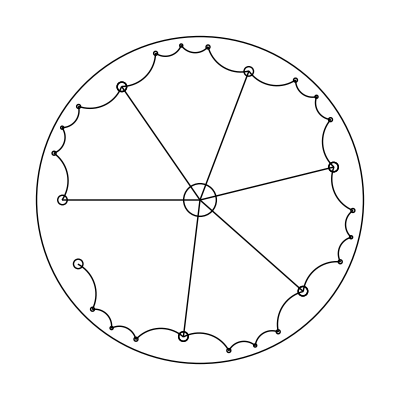

```mathematica
PP=6;QQ=6.5;

({PDiskCircle[#,.2]&/@(Union @@ (Chop[#,10^-5]&/@ #)),


Table[DiskGeodesicArc[{#[[i]],#[[Mod[i,Length[#]]+1]]}],{i,1,Length[#]-1}]&/@#}&@

(Table[#∘Rot[2k Pi/QQ]&/@#,{k,1,QQ}]&@
Table[
0∘Trans[ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘Rot[2k Pi/PP]∘Trans[-ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]],
{k,1,PP}]))//

Graphics[{Circle[{0,0},1],#}]&
```

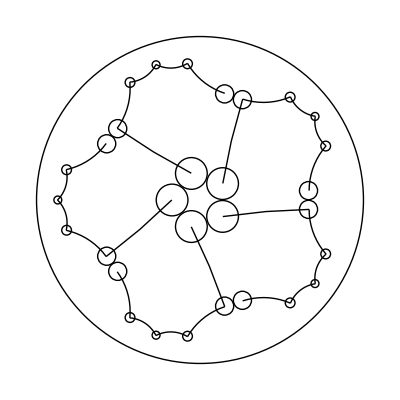

```mathematica
PP=6;QQ=5;

({PDiskCircle[#,.2]&/@(Union @@ (Chop[#,10^-5]&/@ #)),


Table[DiskGeodesicArc[{#[[i]],#[[Mod[i,Length[#]]+1]]}],{i,1,Length[#]-1}]&/@#}&@

(Table[#∘Rot[2k Pi/QQ]&/@#,{k,1,QQ}]&@
Table[
0∘Trans[.77ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘Rot[2k Pi/PP]∘Trans[- ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]],
{k,1,PP}]))//

Graphics[{Circle[{0,0},1],#}]&
```

```mathematica
ArrowHead[{v_,w_},baseWidth_,baseOffset_,topOffset_]:=
DiskGeodesicArc/@
(
Table[RotateRight[#,k]⟦{1,2}⟧,{k,0,Length[#]-1}]&@

(
{0∘Trans[-topOffset]∘#,0∘Trans2Point[0+0I,0+.5I , baseWidth/2]∘Trans[baseOffset]∘#,0∘Trans[baseOffset]∘#,0∘Trans2Point[0+0I,0-.5I , baseWidth/2]∘Trans[baseOffset]∘#}&@
Rot[Arg[v∘Trans2Point[w∘Trans2Point[w,v,DiskDistance[w,v]/2],0]]]∘
Trans2Point[0,w∘Trans2Point[w,v,DiskDistance[w,v]/2]]

)
)
```

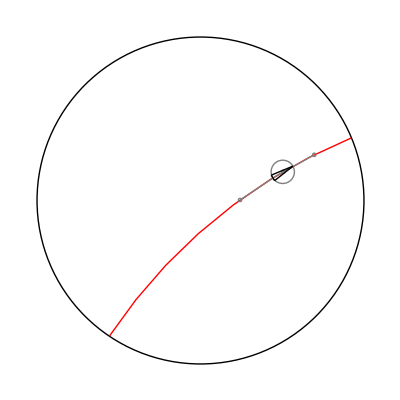

```mathematica
BASEWIDTH=.1;
BASEOFFSET=.2;
TOPOFFSET=.2;

Graphics[{Circle[{0,0},1],
Red,
DiskGeodesic[{0.0001∘#,0∘Trans[ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘#}],
Gray,
DiskGeodesicArc[{0.0001∘#,0∘Trans[ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘#}],

PDiskCircle[0∘Trans[ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]/2]∘#,.2],
Circle[Comp2Real[0∘Trans[ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]/2]∘#],.01],
Circle[Comp2Real[0∘#],.01],
Circle[Comp2Real[0∘Trans[ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘#],.01],

Black,
ArrowHead[{0.00001∘#,0∘Trans[ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘#},BASEWIDTH,BASEOFFSET,TOPOFFSET],

}]&@(Rot[Pi/5]∘Trans[.5])
```

## Misc Graphics Tools

#### Splines, cleanpath

Flower with p fold symmetry, using the spline command:

```mathematica
cleanpath[path_,res_]:=Module[{ppath,i,rr},ppath={path⟦1⟧}; i=0;rr=res^2;
		While[i<Length[path],
			If[#.#&[ppath⟦-1⟧-path⟦i+1⟧]>rr,ppath=Append[ppath,path⟦i+1⟧]];i++];If[Length[ppath]>3,ppath]]
```

```mathematica
cleanpath[path_]:=cleanpath[path,.004]  (* about 1 pt at 3" per unit*)
```

```mathematica
spline[x0_,x1_,v0_,v1_]:=
	a t^3+b t^2 + c t + d/.
		{a->-v1+v0-2x1+2x0,
			b->3x1-3x0-2v0+v1,
			c->v0,d->x0}
```

This is precisely the spline we know and love from Adobe Illustrator:

```mathematica
psBezier[x0_,x1_,c0_,c1_]:=spline[x0,x1,3(c0-x0),3(c1-x1)]
```

This is the ps command produced in eps2eps

```mathematica
rcurve2spline[x0_,y0_,dx1_,dy1_,dx2_,dy2_,dx3_,dy3_]:=
	psBezier[{x0,y0},{x0,y0}+{dx3,dy3},{x0,y0}+{dx1,dy1},{x0,y0}+{dx2,dy2}]
```

this handy command can take a list of rcurves and turn them into a list of points

```mathematica
producePath[{x0_,y0_},curveList_,steps_]:=
	Module[{ss,ii},
		ii=0;
		ss={};
		xi=x0;
		yi=y0;
		While[ii<Length[curveList],
			ii=ii+1;
			ss=Join[ss,
					(rcurve2spline@@Join[{xi,yi},curveList⟦ii⟧])//Table[#/.{t->tt},{tt,0,1,1/(steps+1)}]&];
			xi=xi+curveList⟦ii,5⟧;
			yi=yi+curveList⟦ii,6⟧;
			];
		ss
		]
```

```mathematica
producePath[{x0_,y0_},curveList_]:=producePath[{x0,y0},curveList,10]
```

Show[Graphics[Line[{10,20}+#&/@.2
				producePath[{267.62, 2.89},
{
{-453.34, 633.34, -273.34, 1146.68, 186.66, 940},
{460, -206.67, 1200, 540, 700, 260}
},10]],AspectRatio->Automatic]]

⁃Graphics⁃

#### General commands for drawing motifs

Should clean these up to be more flexible with respect to the model.

```mathematica
DrawMotif[motif_,letter_]:=
Polygon[	cleanpath[Comp2Real[#∘letter⟦2⟧]&/@motif]]
```

```mathematica
DrawMotif[motif_,letter_,f_]:=
f[	cleanpath[Comp2Real[#∘letter⟦2⟧]&/@motif]]
```

```mathematica
DrawMotifK[motif_,letter_]:=
Polygon[	cleanpath[Comp2Real[Poinc2Klein[#∘letter⟦2⟧]]&/@motif]]
```

```mathematica
DrawMotifK[motif_,letter_,f_]:=
f[	cleanpath[Comp2Real[Poinc2Klein[#∘letter⟦2⟧]]&/@motif]]
```

#### Disk Polygon

This takes a list of points in the complex plane, and produces a polygon, with the default resolution; the number of points on a segment is approximately nn per unit of Euclidean distance (1/2nn of an inch on a 4" image)

```mathematica
DiskPolygon[vertexList_]:=Module[{v1,v2,nn},nn=20;
			Comp2Real/@
			(Join@@
			Append[Table[v1=vertexList[[i]];v2=vertexList[[i+1]];
					steps =Ceiling[ nn  (Abs[v1-v2])];
				Table[v1∘Trans2Point[v1,v2,DiskDistance[v1,v2] k/steps],{k,0,steps-1}],{i,1,Length[vertexList]-1}],{vertexList[[-1]]}])]
```

#### Flowers

```mathematica
Flower[p_,v1_,v2_,s1_,s2_,steps_]:=
		Join @@
		((Join[Reverse[Conjugate/@#],#]&[
					(
						Real2Comp/@
							Table[
								spline[
									v1,
									v2,
									s1,
									s2
								],{t,0,1,1/steps}])]
			)//Table[(#∘Rot[2π/p k ])&/@#,{k,1,p}]&)//
		Chop[#,10^-5]&
```

#### feet, petals, faces

```mathematica
foot=cleanpath[.0001 producePath[{1828.66, 2302.77}, {{
-42.42, -296.97, -236.79, -566.53, -371.44, -828.45}, {
-135.99, -264.54, -224.36, -535.78, -333.72, -810.13}, {
-142.84, -358.35, -423.91, -852.24, -873.97, -581.15}, {
-398.66, 240.14, -203.3, 785.68, -146.46, 1147.93}, {
42.25, 269.26, 112.47, 542.07, 139.67, 812.6}, {
35.19, 350.08, -24.57, 728.57, -58.6, 1077.17}, {
-28.72, 294.2, 70.17, 579.87, 74.53, 872.41}, {
3.2, 214.75, -28.57, 511.9, 186.48, 641.98}, {
248.93, 150.57, 512.81, -174.91, 437.54, -413.4}, {
-33.05, -104.7, -107.32, -166.83, -123.09, -276.53}, {
-4.52, -31.7, 10.63, -73.75, 50.57, -66.99}, {
66.3, 11.22, 67.65, 154.61, 82.37, 201.77}, {
51.34, 164.52, 58.03, 569.69, 340.56, 454}, {
252.25, -103.29, -80.46, -392.93, -87.39, -550.3}, {
-4.7, -107.12, 66.92, -103.93, 71.99, 1.5}, {
5.57, 116.2, 78.13, 237.91, 162.82, 314.53}, {
67.68, 61.25, 166.03, 76.64, 217.28, -12.51}, {
64.1, -111.47, -0.48, -213.09, -77.03, -293.77}, {
-39.57, -41.71, -76.89, -91.99, -88.91, -149.26}, {
-14.89, -70.91, 24.15, -106.29, 38.03, -145.37}, {
2.17, -6.11, 4.96, -17.64, 14.72, -13.59}, {
34.2, 102.57, -3.24, 204.77, 75.11, 292.22}, {
93.03, 103.85, 244.44, 39.05, 270.46, -87.77}, {
32.66, -159.2, -319.21, -442.75, -85.66, -583.46}, {
6.27, -3.77, 21.69, 1.84, 20.92, 10.24}, {
-2.16, 4.99, -21.25, 10, -26.25, 21.25}, {
-67.06, 150.89, 6, 222.92, 28.89, 252.32}, {
157.81, 202.64, 256.35, -120.81, 243.09, -242.2}, {
-19.51, -178.55, -44.98, -331.14, -34.79, -513.38}, {
10.92, -195.19, -173.81, -355.72, -147.7, -531.66}}],.002];
```

```mathematica
rock=#+{-.07,.04}&/@ cleanpath[.00011 producePath[{157.7, 1156.19}, {{
-67.41, 128.61, -128.61, 315.38, -147.3, 459.14}, {
-25.58, 196.7, 44, 272.01, 117.56, 440.58}, {
26.19, 60, 31.78, 127.79, 28.26, 192.2}, {
-2.54, 46.44, -41.37, 114.15, -31.22, 159.19}, {
17.6, 78.05, 143.67, 169.27, 198.74, 222.95}, {
112.77, 109.9, 265.84, 184.03, 429.09, 157.4}, {
38.05, -6.21, 69.47, -41.51, 111.31, -51.18}, {
86.22, -19.93, 182.85, 23.97, 268.26, 26.82}, {
170.51, 5.68, 264.88, -76.12, 363.93, -188.06}, {
109.6, -123.86, 207.06, -235.09, 338.66, -343.59}, {
58.33, -48.08, 138.42, -89.19, 192.52, -139.62}, {
107.06, -99.79, 68.55, -189.45, 80.25, -333.73}, {
13.64, -168.22, -14.94, -380.35, 177.19, -423.25}, {
122.81, -27.42, 230.08, 41.01, 288.45, -68.84}, {
39.07, -73.52, 22.23, -330.16, 2.82, -412.69}, {
-24.97, -106.15, -163.39, -188.57, -267.05, -206.14}, {
-3, -93.02, -14.12, -175.26, -33.73, -265.21}, {
-29.75, -136.52, -12.23, -160.55, -150.65, -165.91}, {
-270.06, -10.44, -541.23, 47.33, -812.12, 50.17}, {
-78.49, 0.82, -95.2, 0.02, -157.7, -28.34}, {
-107.2, -48.64, -162.95, -197.66, -278.82, -226.54}, {
-233, -58.1, -388.56, 286.51, -490.01, 432.59}, {
-55.53, 79.95, -114.04, 152.08, -151.76, 242.86}, {
-64.75, 155.82, -38.19, 321.79, -76.69, 469.2}}],.002];
```

```mathematica
petal =  cleanpath[.00014(#-{249.13, 4.25})&/@
			 producePath[{249.13, 4.25},{{
-310, 190, -330, 910, -30, 1040},{
300, 130, 550, -140, 400, -440},{
-150, -300, -410, -260, -370, -600}}],.002];


petal2=cleanpath[.00014(#-{249.13, 4.25})&/@
				 producePath[{1295.85, 1906.25},{{
-625, 218.75, -1630.2, -464.6, -1177.09, -1250},{
312.5, -541.67, 948.09, -397.6, 1104.17, -104.17},{
260.42, 489.59, -968.75, 1291.67, 72.92, 1354.17}}],.001];
```

```mathematica
dragonwickR=

cleanpath[.00014(#-{249.13, 4.25})&/@
				 producePath[{
1556.24, 580.5},{{
111.18, -226.68, -525.28, -305.24, -643.43, -325.78}, {
0, -3.7, 0, -7.41, 0, -11.11}, {
243.3, -87.73, 609.18, -227.44, 833.02, -46.84}, {
98.17, -40.52, -163.67, -180.27, -182.76, -184.71}, {
-134.35, -31.2, -266.24, 2, -390.87, 52.7}, {
-120.28, 48.93, -233.59, 114.36, -347.26, 176.63}, {
-109.42, 28.32, -238.76, -13.28, -353.03, 11.09}, {
108.17, 86.82, 255.81, 22.69, 378.91, 21.48}, {
158.31, 25.34, 325.04, 41.79, 473.11, 107.19}, {
70.55, 31.16, 135.07, 72.43, 188.99, 127.93}, {
-25.18, 50.83, -88.57, 62.93, -136.75, 80.84}, {
-151.49, 56.31, -318.51, 63.2, -478.59, 60.62}, {
-110.73, -1.79, -376.77, 29.87, -431.52, -67.49}, {
-26.69, -137.45, -25.73, -278.25, -31.52, -417.61}, {
-1.73, -41.7, 12.2, -152.75, -38.54, -152.75}, {
-63.5, 0, -66.48, 46.26, -69.29, 97.27}, {
-8.55, 155.75, -65.07, 372.34, 45.36, 492.12}, {
-87.24, -11.82, -173.24, -32.29, -256.58, -60.63}, {
-21.37, -7.27, -115.49, -70.38, -115.49, -12.36}, {
0, 35, 56.14, 55.85, 81.17, 70.11}, {
147.93, 84.27, 318.08, 111.78, 484.19, 135.63}, {
157.43, 22.61, 314.45, 32.35, 473.59, 25.26}, {
142.49, -6.35, 443.8, -30.36, 517.29, -179.61}}],.001];
```

```mathematica
face1=cleanpath[.00011 producePath[{ 694.91, 1534.24}, {{
-3.32, -62.42, -35.78, -99.73, -36.05, -139.57}, {
-0.74, -108.67, 100.55, -203.79, 76.02, -327.15}, {
-10.62, -53.91, -66.99, -109.34, -84.1, -71.95}, {
-99.69, 217.15, 3.13, 503.36, -148.4, 723.04}, {
-83.59, -173.35, -49.37, -300.07, -1.64, -475.19}, {
-54.18, 12.5, -99.3, -33.99, -89.96, -76.21}, {
11.05, -49.88, 94.96, -80.98, 100.59, -126.41}, {
12.19, -96.29, -150.7, 86.06, -139.77, -83.4}, {
10.08, -157.14, 45.63, -309.96, 42.85, -468.67}, {
-0.9, -52.77, -51.05, -110.66, -86.56, -70.31}, {
-363.12, 412.85, -425.07, 1085.16, -185.66, 1599.37}, {
-41.29, 28.36, -80.59, 62.5, -66.56, 127.27}, {
185.78, 856.88, 935.36, 1006.96, 1569.11, 1057.7}, {
177.93, -159.53, 86.21, -498.71, 251.01, -618.75}, {
322.89, -235.2, 410.47, -461.18, 379.77, -768.95}, {
-23.32, -234.06, -7.03, -455.55, -167.93, -325.08}, {
-20.9, -49.88, -72.46, -106.87, -86.57, -71.37}, {
-60.85, 153.75, -15.39, 375, -174.84, 443.68}, {
-31.87, 13.75, -80.51, 12.03, -100.55, -13.01}, {
-151.36, -189.69, -311.32, -289.88, -519.64, -239.65}, {
-10.12, 2.46, -4.34, 78.87, -20.28, 117.66}, {
-20.74, 50.78, -61.17, 81.29, -111.4, 57.14}, {
27.03, 101.84, 191.99, 70.2, 135.07, 216.84}, {
-19.76, 51.06, -60.82, 81.41, -111.09, 57.27}, {
162.38, 166.48, 351.17, 6.25, 538.13, 59.8}, {
-7.5, -66.68, 26.48, -116.64, 68.71, -119.34}, {
15.86, -0.97, 30.78, 39.85, 46.29, 64.34}, {
45, -90.98, 121.56, -73.12, 162.46, -37.89}, {
147.93, 127.07, -69.81, 281.33, -48.05, 458.52}, {
28.67, 235.35, -76.8, -73.44, -129.69, 43.55}, {
-30.66, 67.66, -38.67, 137.03, -63.47, 203.79}, {
-19.11, 51.29, -59.18, 81.33, -110.94, 57.62}, {
-83.05, -38.01, -3.75, -177.15, -85.12, -213.36}, {
-11.99, 72.42, -2.69, 198.24, -71.44, 175.86}, {
-110.47, -36.09, -186.18, -182.62, -306.72, -209.61}, {
-16.33, -3.67, -39.3, 32.46, -59.81, 52.89}, {
-50.08, -134.69, -103.01, -268.01, -116.72, -420.12}, {
-20.59, 20.51, -49.8, 57.78, -56.6, 52.35}, {
-61.02, -47.97, -127.73, -133.6, -128.09, -211.37}, {
-0.66, -171.92, -53.44, -308.99, -62.34, -481.33}}],.002];

face2=cleanpath[.00011 producePath[{ 1185.77, 916.43}, {{
76.72, 210.43, 193.52, 396.21, 398.63, 379.65}, {
-7.38, -66.65, 25.36, -109.77, 69.54, -122.86}, {
73.43, -21.75, 155.66, 57.74, 221.91, -48.24}, {
59.37, 132.81, 149.34, 131.99, 227.73, 108.2}, {
118.29, -35.82, 203.05, -304.6, 132.78, -481.52}, {
-107.23, -269.69, -260.47, -305.23, -412.19, -529.57}, {
-16.21, -24.06, -15.74, -112.69, -52.66, -115.04}, {
-343.2, -21.25, -675.47, -188.63, -1028.95, -58.05}, {
160.94, 131.88, -9.69, 289.5, -52.27, 469.07}, {
137.5, -46.17, 188.95, -218.99, 309.02, -298.48}, {
113.95, -75.43, 188.09, -63.79, 267.47, 83.05}, {
26.44, 49.1, 65.23, 7.73, 50, -52.54}, {
-7.31, -28.63, -40.35, -51.68, -37.35, -73.32}, {
14.65, -105.78, 136.92, -14.3, 170.08, -117.07}, {
71.88, 174.65, 95.04, 364.76, 216.84, 499.14}, {
-107.15, 103.16, -241.1, 120.23, -360.24, 217.07}, {
-73.04, 59.3, -9.14, -261.21, -127.97, -122.42}, {
-47.07, 54.88, -27.53, 166.6, 7.62, 262.93}}],.002];
```

```mathematica
swanBlob = cleanpath[.00011 producePath[{595.14, 1716.47},{{
228.3, 64.26, 366.58, 255.09, 498.16, 438.55}, {
70.68, 98.54, 242.12, 269.04, 379.15, 249.96}, {
-116.77, -88.33, -268.28, -215.21, -275.95, -373.69}, {
107.89, -28.5, 162.64, -117.71, 133.5, -220.57}, {
-57.67, -203.52, -303.81, -192.27, -479.09, -232.36}, {
-93.3, -21.35, -250.36, -49.3, -289.3, -152.81}, {
-45.57, -121.11, 80.35, -205.07, 189.54, -209.52}, {
98.95, -4.04, 194.73, 41.82, 296.93, 31.31}, {
116.26, -11.96, 250.59, -64.65, 345.72, -134.16}, {
353.9, -258.56, 37.42, -808.1, -241.45, -974.7}, {
-245.59, -146.71, -725.14, -204.07, -956.41, -6.64}, {
-126.81, 108.26, -217.19, 292.63, -184.04, 461.56}, {
37, 188.55, 197.55, 289.37, 174.01, 501.66}, {
-15.75, 142.03, -78.65, 248.52, -16.3, 393.13}, {
79.56, 184.55, 256.12, 180.61, 425.53, 228.28}}],.002];
```

Show[Graphics[{Line[foot],Line[petal],Line[petal2],Line[rock]},AspectRatio->Automatic,Axes->True]]

⁃Graphics⁃

Show[Graphics[{Line[face1],Line[face2],Line[dragonwickR]},AspectRatio->Automatic,Axes->True]]

⁃Graphics⁃

Show[Graphics[{Line[swanBlob]},AspectRatio->Automatic,Axes->True]]

⁃Graphics⁃

#### callaLily

```mathematica
calla[1]={
{407.06, 3840.05}, {{
18.25, -13.7, 25.66, -134.21, 26.52, -174.34}, {
0.86, -40.14, -115.21, -723.94, -177.11, -1363.49}, {
-61.89, -639.55, -144.72, -1934.63, -138.53, -1987.21}, {
6.19, -52.58, 99.65, -243.17, 91.71, -280.21}, {
-7.94, -37.04, -53.81, -47.05, -78.79, -26.08}, {
-24.98, 20.98, -80.7, 82.3, -86.38, 316.95}, {
-5.65, 234.64, 272.23, 3374.5, 271.77, 3337.2}, {
-0.46, -37.3, -1.02, 162.73, 26.64, 183.64}, {
27.66, 20.91, 45.92, 7.23, 64.17, -6.46}},.01
};

calla[2]={
{738.83, 5271.61}, { {
				58.09, 111.36, 86.23, 202.18, 59.43, 278.09}, {
-37.5, 106.25, -222.79, 135.52, -246.87, 153.13}, {
-23.26, 17.01, -21.87, 18.75, -21.87, 37.5}, {
0, 18.75, -12.5, 50, -25, -3.12}, {
-12.5, -53.12, -40.71, -63.09, -112.5, -34.37}, {
-78.12, 31.25, -368.75, -25, -384.37, -206.25}, {
-5.83, -67.66, -15.12, -95.06, 1.77, -152.79}, {
16.89, -57.73, 238.89, -623.57, 279.48, -634.71}, {
40.59, -11.13, 184.8, 138.24, 206.25, 159.38}},.003};






calla[3]={
{360.76, 4962.2}, {{
8.88, 48.86, -15.62, 153.13, 31.25, 146.88}, {
46.88, -6.25, 53.13, -34.37, 56.25, -71.87}, {
3.13, -37.5, 7.79, -114.68, 6.25, -143.75}, {
-1.54, -29.07, -43.46, -90.52, -62.5, -90.62}, {
-19.04, -0.11, -40.13, 110.52, -31.25, 159.38}},.005
};

calla[4]={
{9.4, 5343.79}, {{
50, -168.75, 248.23, -859.71, 288.86, -894.09}, {
40.63, -34.38, 230.71, 458.65, 196.88, 462.5}, {
-33.84, 3.86, -229.18, 138.57, -350, 259.38}, {
-53.16, 53.16, -114.72, 102.85, -135.73, 172.21}},.01
};

calla[5]=
{
{738.83, 5271.61}, {{
-53.02, -100.08, -149.91, -224.23, -315.57, -378.16}, {
-353.12, -328.13, -390.62, -403.13, -390.62, -509.38}, {
0, -106.25, 171.88, -265.62, 234.38, -393.75}, {
62.5, -128.12, 75.13, -97.39, 62.63, -169.27}, {
-12.5, -71.87, 0, -51.67, 9.25, -65.1}, {
15.85, -23.02, 46.88, -12.5, 65.63, 15.62}, {
18.75, 28.13, 101.98, 194.84, 115.63, 293.75}, {
12.5, 90.63, 9.38, 228.13, 25, 350}, {
15.63, 121.88, 18.75, 246.88, 43.75, 318.75}, {
25, 71.88, 121.82, 471.92, 149.94, 537.54}},.01
};
```

```mathematica
callaOutlineColors={{106, 141, 31},
{194, 194, 170},
{157, 111, 17},{194, 194, 170},{194, 194, 170}


	}/255;
```

```mathematica
callaColors= {
	{138,181,22},{255,255,240},{248,171,0},{248,248,225},{243,243,212}}/255;

CallaLily=Table[cleanpath[.00011 producePath[#⟦1⟧,#⟦2⟧	],#⟦3⟧]& [ calla[i]],{i,1,5}];
```

Show[Graphics[Join[{GrayLevel[.2],Polygon[{{0,0},{0,.8},{.2,.8},{.2,0}}]},
		
		
		Table[{RGBColor @@(callaColors[[i]]),Polygon[CallaLily[[i]]]},{i,1,5}]],
			
			
			AspectRatio->Automatic,Axes->True]]

⁃Graphics⁃

# more stuff

Playing with 7,3 and drawing the Klein Quartic

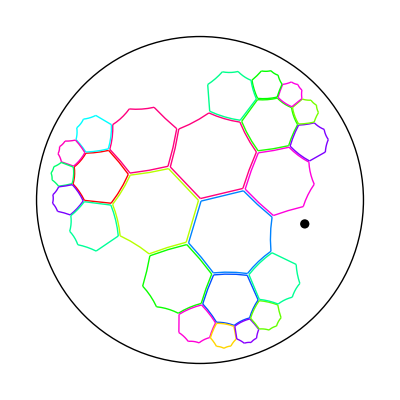

```mathematica
PP=7;QQ=3; (*change at will*)
longdiagonal=ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]];
shortdiagonal=ArcCosh[Cos[Pi/3]/Sin[Pi/7]];
halfedge=ArcCosh[Cos[Pi/7]/Sin[Pi/3]];
gon = Table[
0∘Trans[.97 ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘Rot[2k Pi/PP],
{k,1,PP}];

ashift=0∘Trans[longdiagonal]∘Rot[2Pi/7]∘Trans[2shortdiagonal]∘Rot[-Pi/7];




gons = movestuff[gon,
Join[{Trans[0]},Table[
Trans[ArcCosh[Cos[Pi/3]/Sin[Pi/7]]]∘Trans[shortdiagonal]∘Rot[Pi/7]∘Rot[2Pi k/7],
{k,0,6}]
]];

ggons = movestuff[#,Table[Trans2Point[ashift,0]∘Rot[2Pi k/3],{k,0,2}]]&/@gons//Join@@#&;

Graphics[{Circle[{0,0},1],
Table[
{Hue[Random[]],
Table[
DiskGeodesicArc[{gon[[i]],gon[[Mod[i,PP]+1]]}],{i,PP}]},{gon, ggons}],
PDisk[0∘Trans[longdiagonal]∘Rot[2Pi/7]∘Trans[2shortdiagonal]∘Rot[-Pi/7],.1]
}]
```

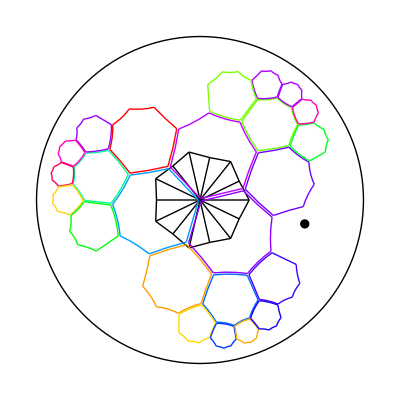

```mathematica
PP=7;QQ=3; 
longdiagonal=ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]];
shortdiagonal=ArcCosh[Cos[Pi/3]/Sin[Pi/7]];
halfedge=ArcCosh[Cos[Pi/7]/Sin[Pi/3]];

flag = {0,0∘Trans[longdiagonal],0∘Trans[shortdiagonal]∘Rot[Pi/7]};
frag = {0,0∘Trans[shortdiagonal]∘Rot[-Pi/7],0∘Trans[longdiagonal]};

gon = Table[
0∘Trans[.97 ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘Rot[2k Pi/PP],
{k,1,PP}];

ashift=0∘Trans[longdiagonal]∘Rot[2Pi/7]∘Trans[2shortdiagonal]∘Rot[-Pi/7];


flags = movestuff[flag,Table[Rot[2Pi/7 k],{k,0,6}]];
frags = movestuff[frag,Table[Rot[2Pi/7 k],{k,0,6}]];

gons = movestuff[gon,
Join[{Trans[0]},Table[
Trans[ArcCosh[Cos[Pi/3]/Sin[Pi/7]]]∘Trans[shortdiagonal]∘Rot[Pi/7]∘Rot[2Pi k/7],
{k,0,6}]
]];

ggons = movestuff[#,Table[Trans2Point[ashift,0]∘Rot[2Pi k/3],{k,0,2}]]&/@gons//Join@@#&;

Graphics[{Circle[{0,0},1],
drawpoly/@flags,drawpoly/@frags,
Table[
{Hue[Random[]],
Table[
DiskGeodesicArc[{gon[[i]],gon[[Mod[i,PP]+1]]}],{i,PP}]},{gon, ggons}],
PDisk[0∘Trans[longdiagonal]∘Rot[2Pi/7]∘Trans[2shortdiagonal]∘Rot[-Pi/7],.1]
}]
```

```mathematica
PP=7;QQ=3; 
longdiagonal=ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]];
shortdiagonal=ArcCosh[Cos[Pi/3]/Sin[Pi/7]];
halfedge=ArcCosh[Cos[Pi/7]/Sin[Pi/3]];

edgecenter=0∘Trans[shortdiagonal]∘Rot[Pi/7];
neighboringcenter=0∘Trans[2shortdiagonal]∘Rot[Pi/7];

backpoint = 0∘Trans[-shortdiagonal];

flag = {0,0∘Trans[longdiagonal],0∘Trans[shortdiagonal]∘Rot[Pi/7]};
frag = {0,0∘Trans[shortdiagonal]∘Rot[-Pi/7],0∘Trans[longdiagonal]};

triangle = {0∘Trans[shortdiagonal]∘Rot[Pi/7],0∘Trans[shortdiagonal]∘Rot[-Pi/7],0∘Trans[longdiagonal+halfedge]};




gon = Table[
0∘Trans[.97 ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘Rot[2k Pi/PP],
{k,1,PP}];

ashift=0∘Trans[longdiagonal]∘Rot[2Pi/7]∘Trans[2shortdiagonal]∘Rot[-Pi/7];


flags = movestuff[flag,Table[Rot[2Pi/7 k],{k,0,6}]];
frags = movestuff[frag,Table[Rot[2Pi/7 k],{k,0,6}]];

fflags = movestuffs[flags,Join[{Trans[0.]},Table[RotAboutPt[0∘Trans[shortdiagonal]∘Rot[Pi(2k+1)/7],Pi],{k,0,6}]]];
rflags = movestuffs[frags,Join[{Trans[0.]},Table[RotAboutPt[0∘Trans[shortdiagonal]∘Rot[Pi(2k+1)/7],Pi],{k,0,6}]]];


gons = movestuff[gon,
Join[{Trans[0]},Table[
Trans[ArcCosh[Cos[Pi/3]/Sin[Pi/7]]]∘Trans[shortdiagonal]∘Rot[Pi/7]∘Rot[2Pi k/7],
{k,0,6}]
]];

ggons = movestuff[#,Table[Trans2Point[ashift,0]∘Rot[2Pi k/3],{k,0,2}]]&/@gons//Join@@#&;

star = movestuff[triangle,Table[Rot[2Pi k/7],{k,0,6}]];


star2 = movestuffs[star,Join[ {Trans[0]},Table[
	RotAboutPt[0∘Trans2Point[0,star[[1,3]]],Pi]∘Rot[2Pi k/7],{k,0,6}]]];

tt=Join@@ movestuff[star2[[14]],{RotAboutPt[0∘Trans2Point[0,star2[[14,3]]],Pi]}];
tt2 = movestuff[tt,{Trans[0],RotAboutPt[tt[[1]],Pi]}];
tts = Join @@(movestuff[#,Table[Rot[2Pi k/7],{k,0,6}]]&/@tt2);

colors=Table[Hue[i/7],{i,0,7}];
colors = {Hue[0],Hue[Rational[1, 7], 1, 0.9400000000000001],Hue[0.1, 1., 0.9500000000000001],Hue[0.33, 1., 0.47000000000000003],Hue[0.54, 0.9400000000000001, 0.92],Hue[Rational[5, 7], 1, 0.8],Hue[Rational[6, 7], 0.84, 0.85],Hue[0.35000000000000003, 0.77, 0.8]};
colors2={Hue[Rational[1, 7], 0.13, 0.68],Hue[0.66, 0.03, 0.9400000000000001]};

arc1 = {star2[[20,3]],star2[[52,3]]};
arc2 = {tts[[14,2]],tts[[8,3]]};
arc3={star2[[12,3]],star2[[18,3]]};
arc4={star2[[11,3]],star2[[13,3]]};
arc5={star2[[10,3]],star2[[12,3]]};

bands={i=1;
{colors[[i++]],DiskGeodesicArc[#]}&/@movestuff[arc1,Table[Rot[2Pi k/7],{k,0,6}]],
i=1;{colors[[i++]],DiskGeodesicArc[#]}&/@movestuff[arc2,Table[Rot[2Pi (k+4)/7],{k,0,6}]],
i=1;{colors[[i++]],DiskGeodesicArc[#]}&/@movestuff[arc3,Table[Rot[2Pi (k+2)/7],{k,0,6}]],
i=1;{colors[[i++]],DiskGeodesicArc[#]}&/@movestuff[arc5,Table[Rot[2Pi (k)/7],{k,0,6}]],
i=1;{colors[[i++]],DiskGeodesicArc[#]}&/@movestuff[arc4,Table[Rot[2Pi (k+5)/7],{k,0,6}]],

i=1;{colors[[i++]],
DiskGeodesicArc[#]}&/@Table[{arc2[[2]]∘Rot[2Pi k/7],
 arc2[[1]]∘Rot[2Pi (k+1)/7]},{k,0,6}]
};


ringflags=movestuff[flag,Table[RotAboutPt[0∘Trans[shortdiagonal]∘Rot[Pi/7],Pi]∘Rot[2k Pi/7],{k,0,6}]];
rringflags=movestuff[frag,Table[Rot[2Pi/7]∘RotAboutPt[edgecenter,Pi]∘Rot[2k Pi/7],{k,0,6}]];
```

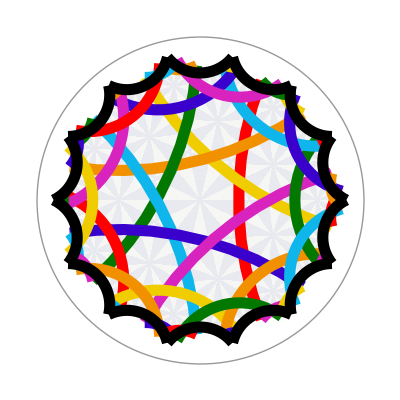

```mathematica
Graphics[{
GrayLevel[0.6],
Circle[{0,0},1],

colors2[[1]],
Opacity[.1],

Polygon[drawrpoly@#]&/@
(( movestuffs[
Join[
(*a flag*)
#[[{1}]],
(*outer ring*)
movestuffs[#, {RotAboutPt[0∘Trans[longdiagonal+halfedge],Pi]}],

(*outer pair*)
movestuffs[#[[{7,1,2}]],{RotAboutPt[neighboringcenter,2Pi 3/7]}],
movestuffs[#[[{7,1,2,3}]],{RotAboutPt[neighboringcenter,2Pi 4/7]}],
(*spiky bit*)
movestuff[#[[1]],{Rot[2Pi/7]∘RotAboutPt[edgecenter,Pi]∘Rot[4Pi/7]∘RotAboutPt[neighboringcenter,4 2Pi/7]}],
(*center and inner ring*) 
movestuffs[#,{RotAboutPt[0∘Trans[shortdiagonal]∘Rot[Pi/7],Pi]}],
movestuff[#[[4]],{Trans[2(shortdiagonal+longdiagonal+halfedge)]}]
]
,Table[Rot[2Pi k/7],{k,0,6}]]
)&@
(*flags*) movestuff[#,Table[Rot[2Pi/7 k],{k,0,6}]]&@flag),

colors2[[2]],
Opacity[1],

Polygon[drawrpoly@#]&/@
(( movestuffs[
Join[
(*a flag*)
#[[{1}]],
(*outer ring*)
movestuffs[#, {RotAboutPt[0∘Trans[longdiagonal+halfedge],Pi]}],

(*outer pair*)
movestuffs[#[[{7,1,2,3}]],{RotAboutPt[neighboringcenter,2Pi 3/7]}],
movestuffs[#[[{1,2,3}]],{RotAboutPt[neighboringcenter,2Pi 4/7]}],
(*spiky bit*)
movestuff[#[[1]],{Rot[2Pi/7]∘RotAboutPt[edgecenter,Pi]∘Rot[4Pi/7]∘RotAboutPt[neighboringcenter,4 2Pi/7]}],
(*center and inner ring*) 
movestuffs[#,{RotAboutPt[0∘Trans[shortdiagonal]∘Rot[Pi/7],Pi]}],
movestuff[#[[5]],{Trans[2(shortdiagonal+longdiagonal+halfedge)]}]
]
,Table[Rot[2Pi k/7],{k,0,6}]]
)&@
(*flags*) movestuff[#,Table[Rot[2Pi/7 k],{k,0,6}]]&@frag),



Thickness[.02],Opacity[1],
bands,

Black,
Thin,
Table[DiskGeodesicArc[{#[[i]],#[[i+1]]}],{i,Length[#]-1}]&@(#[[1]]&/@movestuff[flag,Table[Rot[2Pi/7]∘RotAboutPt[edgecenter,Pi]∘Rot[4Pi/7]∘RotAboutPt[neighboringcenter,4 2Pi/7]∘Rot[j  Pi/7],{j,0,14}]]),



}]
```

```mathematica
DiskAngleBetwixt[edgecenter, edgecenter∘Rot[-2Pi/7], edgecenter∘RotAboutPt[0∘Trans[longdiagonal],2Pi/3]] /Pi 180
```

-120.712

```mathematica
DiskAngleBetwixt[edgecenter, edgecenter∘Rot[-2Pi/7], edgecenter∘RotAboutPt[0∘Trans[longdiagonal],4Pi/3]]/Pi 180
```

-58.0569

Substitutions

```mathematica
(* As Transforms*)
```

```mathematica
Clear[subtodepth,subonlytodepth];
subtodepth[generators_,0,start_:{Ident}]:=start;
subtodepth[generators_,depth_,start_:{Ident}]:=subtodepth[generators,depth,start]=Union[#,
SameTest->(Round[#1,10^-6]===Round[#2,10^6]&)]&@@Outer[#1∘#2&,subtodepth[generators,depth-1,start],generators];
subonlytodepth[generators_,depth_,start_:{Ident}]:=subonlytodepth[generators,depth,start]=Complement[ subtodepth[generators,depth,start], subtodepth[generators,depth,start]-1]
```

We will do depth first substitutions.

```mathematica
SubIt[rules_,start_,applyRulesMethod_, maxdepth_,stopTest_,same_:Join]:=
	same@@(SubIt[rules,#,applyRulesMethod,maxdepth-1,stopTest]&/@((applyRulesMethod[rules,#])&/@ Select[start,stopTest]))

SubIt[_,a_,_,0,_]:=a
```

Everything that appears needs to have a rule assigned to it.

A default stop function

```mathematica
stopFunction[tolerance_][letter_]:=(Abs[0∘letter⟦2⟧]<(1-tolerance))
```

#### examples

(StringJoin[ToString/@#]&/@

Table[SubIt[
	{{a,{c,a,a}},{b,{b,c,b}},{c,{x,x,a}},{x,{y}}
	},
	{a},
		(#2/.((#⟦1⟧->#⟦2⟧)&/@#1))&,		
i,
!(y===#)&],{i,1,4}])//TableForm

caa
xxacaacaa
yycaaxxacaacaaxxacaacaa
xxacaacaayycaaxxacaacaaxxacaacaayycaaxxacaacaaxxacaacaa

```mathematica
Clear[word,rules]
```

SubIt[
{
		{X,
			{
				{X,Mobius[RotAboutPt[1+I,π/3]]},
				{Y,Mobius[RotAboutPt[-I-.4,π/9]]}
			}}
		,{Y,
			{
				{X,Mobius[RotAboutPt[.2,π]]}}}},
	{{X,Mobius[|1,0|]}},
	
	
Module[{word,rules},
		word=#2;
		rules = #1;

			{#⟦1⟧,word⟦2⟧∘#⟦2⟧}&/@
				
				(Select[rules,#⟦1⟧===word⟦1⟧&][[1,2]])]&,
	
	3,True&]

{{X,Mobius[{{0.+3. I,2.-2. I},{2.+2. I,0.-3. I}}]},{Y,Mobius[{{1.73785+0.957838 I,-0.911309-1.75542 I},{-0.911309+1.75542 I,1.73785-0.957838 I}}]},{X,Mobius[{{0.427028-1.23953 I,-0.662794+1.12067 I},{-0.662794-1.12067 I,0.427028+1.23953 I}}]},{X,Mobius[{{0.427028-0.0541979 I,0.281594+0.287058 I},{0.281594-0.287058 I,0.427028+0.0541979 I}}]},{Y,Mobius[{{0.140442-0.307685 I,0.309546-0.134058 I},{0.309546+0.134058 I,0.140442+0.307685 I}}]}}

Octopeda

#### intro

We will work with "octopusses"; these will help us with other tasks as well.


We define the name of a given octopus. The indices are a list of legs.

The geometry of the octopus is given by the length of each leg and the angle of each corner. 

 Each leg is of the form 
	shift-to-mate, orientation, order of next face clockwise , name of leg (to look up length), name of corner (to look up angle)
	
All octopusses are read clockwise, with indices running from 1 to length.

For the moment we are assuming the data is given to us correctly.  We are not making any attempt to systemize these calculations at the moment.

We will use the following octopus, which yields the Cayley graph of the group presented as
<α, β, γ, Z | α^2,  β^3, α β γ ,  γ=Z^2 > , the symmetry group of 23x. 



Reading clockwise from α, we have

### Getting some geometry

Working modulo n

```mathematica
a_⋄n_:=Mod[a-1,n]+1
```

For tGp, the tiles are all triangles, with valence 7; so we will cheat.

```mathematica
rotAboutMidPointLeg[length_,argument_]:=
	Mobius[Rot[-argument]]∘Mobius[Trans[-length/2]]∘Mobius[Rot[π]]∘Mobius[Trans[length/2]]∘Mobius[Rot[argument]]
```

```mathematica
refAcrossMidPointLeg[length_,argument_]:=
	Mobius[Rot[-argument]]∘Mobius[Trans[-length/2]]∘Mobius[Rot[π/2]]∘Mobius[Refx]∘Mobius[Rot[-π/2]]∘Mobius[Trans[length/2]]∘Mobius[Rot[argument]]
```

```mathematica
translateDownLeg[length_,arg1_, arg2_]:=
	Mobius[Rot[-arg1+π]]∘Mobius[Trans[length]]∘Mobius[Rot[arg2]]
```

```mathematica
glideReflectDownLeg[length_,arg1_, arg2_]:=
	Mobius[Rot[-arg1+π]]∘Mobius[Refx]∘Mobius[Trans[length]]∘Mobius[Rot[arg2]]
```

```mathematica
AddTransforms[name_]:=
	(indices[name]=Table[
	ReplacePart[indices[name]⟦i⟧,
	getTransform[name,indices[name]⟦i⟧,i]//Chop[#,10^-6]&,4],
	
	{i,1,Length[indices[name]]}])
```

```mathematica
getTransform[name_,index_,i_]:=
	Which[
		index⟦1⟧===0 && index⟦2⟧===1,
		rotAboutMidPointLeg[legLengths[name]⟦i⟧,vertexAngles[name]⟦i⟧],
		
		index⟦1⟧===0 && index⟦2⟧===-1,
		refAcrossMidPointLeg[legLengths[name]⟦i⟧,vertexAngles[name]⟦i⟧],
		
		(!(index⟦1⟧===0)) && index⟦2⟧===1,
		translateDownLeg[legLengths[name]⟦i⟧,vertexAngles[name]⟦(i+index⟦1⟧)⋄Subscript[ℒ, name]⟧,
			vertexAngles[name]⟦i⟧],
		
		(!(index⟦1⟧===0)) && index⟦2⟧===-1,
		glideReflectDownLeg[legLengths[name]⟦i⟧,vertexAngles[name]⟦(i+index⟦1⟧)⋄Subscript[ℒ, name]⟧,
			vertexAngles[name]⟦i⟧]
		]
```

### indices

The basic rules for manipulating indices:

```mathematica
resetIndices := (
		
		Clear[indices];


indices[-name_]:=indices[-name]=
		Table[

			{Mod[1-k,Length[indices[name]]]+1,
				Mod[-k,Length[indices[name]]]+1}
			
			//
			{-(indices[name])⟦#⟦1⟧,1⟧,
					(indices[name])⟦#⟦1⟧,2⟧,
					(indices[name])⟦#⟦2⟧,3⟧,
				  (indices[name])⟦#⟦1⟧,4⟧,
					(indices[name])⟦#⟦2⟧,5⟧
				}&
			,
		{k,1,Length[indices[name]]}
			];

indices[name_+n_Integer]:=RotateRight[indices[name],n]);

resetIndices
```

A motif has the following data: 

Motif[indicesName,baseNum, orientation, shift, position]

indicesName: The name used to look up the indices

basenum: how many of the first faces (after leg 1) are "internal 
	(For example, for an X, baseNum is 3, for a Y, basenum is 2)
	
orientation & leg tells how to adjust the indices 
(so the indices are indices[orientation*indicesName + leg-1])
(leg is the original index of ori*name of the leg that is now in position 1.

position is geometric data.



We move from one motif to another around a face using NextMotif. We may presume that both of these are shifted so that the first legs are those at the face.

```mathematica
NextMotif[Motif[name_,baseN_,ori_,leg_,pos_]]:=
Module[{curIndices,nleg,nori},
		
		curIndices = indices[ori*name+1-leg];
		nleg= Mod[curIndices⟦1,1⟧,Subscript[ℒ, name]];
		nori= ori*curIndices⟦nleg+1,2⟧;
		nleg=(ori*nori(nleg+leg-1))⋄Subscript[ℒ, name];
	
	Motif[name,2,nori, nleg,	Mobius[indices[ori name]⟦leg,4⟧]∘Mobius[pos]]
		
		]
```

FanOutFace expands a motif, out along a leg, creating a list of motifs that wrap counterclockwise around a face.  We know to stop when we return to a Motif of the same name, orientation and shift, for the nth time

leg is counted from Lleg = 1, 
 inFaces describes how many faces are already accounted for at this particular face.  (So for an XY tiling, inFaces is 1 or 2; for triangle tilings, inFaces is 2 or 3.)

keep pos from the _unshifted_ motifs?

```mathematica
FanVertexFrom[leg_,Motif[name_,baseNum_,ori_,Rightleg_,pos_]]:=
	Module[{},
		startMotif=
			nxtMotif=Motif[name,2,ori,(leg+Rightleg-1)⋄Subscript[ℒ, name], pos];
		(*Print[(leg+Rightleg-1)⋄Subscript[ℒ, name]];*)
		cnt=0; maxCount = 10;
		repeats = indices[ori name]⟦(leg+Rightleg-1)⋄Subscript[ℒ, name],3⟧;
	(* Print[repeats];
		Print[indices[ori name]];*)
		repeatCnt=0;
		ss={};
		While[repeatCnt<repeats && cnt<maxCount,
			
			cnt=cnt+1;
			ss=Append[ss,(nxtMotif=NextMotif[nxtMotif])];
			If[nxtMotif⟦{3,4}⟧===startMotif⟦{3,4}⟧ ,
				repeatCnt=repeatCnt+1]
			];
	
(*		Print[repeats," ",Length[ss]];*)
		(*we assume that all fans are really of at least size three*)
		If[Length[ss]<3,Print["rule was supposed to be longer!"];ss={},
			ss=Drop[ Drop[ss,-1],-1]];
		ss⟦1,2⟧=3;
		(*Print["ss ",ss];*)
		ss
			]
```

```mathematica
FullFanVertexFrom[leg_,Motif[name_,baseNum_,ori_,Rightleg_,pos_]]:=
	Module[{},
		startMotif=
			nxtMotif=Motif[name,2,ori,(leg+Rightleg-1)⋄Subscript[ℒ, name], pos];
		(*Print[(leg+Rightleg-1)⋄Subscript[ℒ, name]];*)
		cnt=0; maxCount = 10;
		repeats = indices[ori name]⟦(leg+Rightleg-1)⋄Subscript[ℒ, name],3⟧;
(*		Print[repeats];
		Print[indices[ori name]];*)
		repeatCnt=0;
		ss={};
		While[repeatCnt<repeats && cnt<maxCount,
			
			cnt=cnt+1;
			ss=Append[ss,(nxtMotif=NextMotif[nxtMotif])];
			If[nxtMotif⟦{3,4}⟧===startMotif⟦{3,4}⟧ ,
				repeatCnt=repeatCnt+1]
			];
	
		ss
			]
```

```mathematica
MotifRule[Motif[name_,baseNum_,ori_,Rightleg_,pos_]]:=
	Module[{rr},rr=Join@@
		Table[FanVertexFrom[kk,Motif[name,baseNum,ori,Rightleg,pos]],
			
			{kk,baseNum+1,Subscript[ℒ, name]}];
		(*Print[rr];*)
		If[(Length[rr]>0)&&(baseNum!=0),rr=Drop[rr,-1];(*Print[indices[ori name]⟦(Rightleg+baseNum-1)⋄Subscript[ℒ, name]⟧];*)
			If[Times@@(indices[ori name]⟦(Rightleg+baseNum-1)⋄Subscript[ℒ, name]⟧⟦{3,5}⟧)===3,(*Print["changing"];*)
				rr⟦1,2⟧=4]
		(*	,If[Length[rr]==0,Print["uhoh\n"];
			
			Print[baseNum," ",ori," ", Rightleg," ",pos,"\n"];]*)
			
			
			];rr//Chop[#,10^-6]&]
```

#### examples

These don't make any geometric sense, but show how the indices and rules work:

legLengths["4O"]=Table[2ArcCosh[Cos[π/4]/Sin[π/6]]//N,{k,1,6}];

vertexAngles["4O"]=Table[2π/6. k,{k,0,5}];

indices["4O"]=
	{{-1,1,1,|1,0|,2},
		{2,1,1,|1,0|,2},
		{2,1,1,|1,0|,2},
		{-2,1,1,|1,0|,2},
		{-2,1,1,|1,0|,2},
		{1,1,4,|1,0|,2}};

ℒ_("4O")=Length[indices["4O"]];
AddTransforms["4O"];

FanVertexFrom[5,Motif["tGp",2,1,2,Ident]]

{Motif[tGp,3,-1,3,Mobius[{{-0.5+1.03826 I,0.558341-0.127438 I},{0.558341+0.127438 I,-0.5-1.03826 I}}]]}

Drop[#,-1]&/@FanVertexFrom[1,Motif["4O",2,-1,1,Ident]]

{Motif[4O,3,-1,1],Motif[4O,2,-1,1]}

Drop[#,-1]&/@MotifRule[Motif["4O",3,1,5,Ident]]//Chop[#,10^-6]&

{Motif[4O,3,1,3],Motif[4O,2,1,4],Motif[4O,2,1,1],Motif[4O,3,1,4],Motif[4O,2,1,1],Motif[4O,2,1,5],Motif[4O,3,1,1],Motif[4O,2,1,5]}

MotifRule[Motif["tGp",3,1,2,Ident]]

{Motif[tGp,4,-1,2,Mobius[{{0.5+1.03826 I,0.558341-0.127438 I},{0.558341+0.127438 I,0.5-1.03826 I}}]],Motif[tGp,3,-1,3,Mobius[{{-0.5+1.03826 I,0.558341-0.127438 I},{0.558341+0.127438 I,-0.5-1.03826 I}}]],Motif[tGp,3,1,3,Mobius[{{-0.5+1.03826 I,0.558341-0.127438 I},{0.558341+0.127438 I,-0.5-1.03826 I}}]]}

### Drawing Stuff

```mathematica
BasicDrawMotif[Motif[name_,a_,b_,c_,pos_]]:=
	Join @@ Table[{Hue[i/7],DiskGeodesicArc[{0∘pos,(0)∘Mobius[Trans[legLengths[name]⟦i⟧/2 *1(*.97*)]]∘Mobius[Rot[vertexAngles[name]⟦i⟧]]∘pos}]},{i,1,Length[indices[name]]}]
```

A useful shortcut. ssixe, scootch and themotif are presumed to be defined.

```mathematica
drawit:=DrawMotif[(#∘scootch)&/@(Real2Comp/@ (ssize themotif)),{{},#⟦5⟧}]&/@tiling
```

#### basic drawing examples

Table[Show[Graphics[
		Join [{Circle[{0,0},1]},
	BasicDrawMotif[Motif["4O",3,1,1,Rot[.01]]],
		{Hue[.3]},
		Join@@(BasicDrawMotif/@FanVertexFrom[iXi,Motif["4O",2,1,1,Ident]])],AspectRatio->Automatic,PlotRange->All]],
	{iXi,1,(*6*)1}]

{⁃Graphics⁃}

Table[Show[Graphics[
		Join [{Circle[{0,0},1]},
	BasicDrawMotif[Motif["tGp",1,1,1,Ident]],
		{Hue[.3]},
		Join@@(BasicDrawMotif/@MotifRule[Motif["tGp",2,1,ii,Ident]])],AspectRatio->Automatic,PlotRange->All]],
	{ii,1,(*7*)1}]

{⁃Graphics⁃}

Show[Graphics[Join[
		BasicDrawMotif[Motif["tGp",1,1,1,Ident]],
			Join @@ Table[
					
					BasicDrawMotif[Motif["tGp",1,1,1,indices["tGp"]⟦i,4⟧]],{i,1,7}]],AspectRatio->Automatic]]

⁃Graphics⁃

### octopus subst functions

```mathematica
stopFunction[tolerance_][Motif[name_,a_,b_,c_,pos_]]:=(Abs[0∘pos]<(1-tolerance))
```

```mathematica
octopusRuleApplication=Module[{word,rules},
		
		word=#2;
		name = #1;

	MotifRule[#2]
	
	
	]&
```

Module[{word,rules},word=#2;name=#1;MotifRule[#2]]&

### 444

```mathematica
legLengths["tGp"]=Table[2ArcCosh[Cos[π/3]/Sin[π/8]]//N,{k,1,8}];
vertexAngles["tGp"]=Table[2π/8. k,{k,0,6}];


	

indices["tGp"]=Table[{0,1,1,,3},{i,1,6}];

Subscript[ℒ, "tGp"]=Length[indices["tGp"]];
AddTransforms["tGp"];

sstart=ReplacePart[MotifRule[Motif["tGp",-1,1,1,
				Rot[Pi/8]∘Trans[ArcCosh[Cot[Pi/8] Cot[Pi/3]]]
			
			]],3,{1,2}];
tiling= 
	
	(tXX={Motif["tGp",-1,0,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
0,
	stopFunction[.1]],tXX]);
```

```mathematica
Length[tiling]
```

28

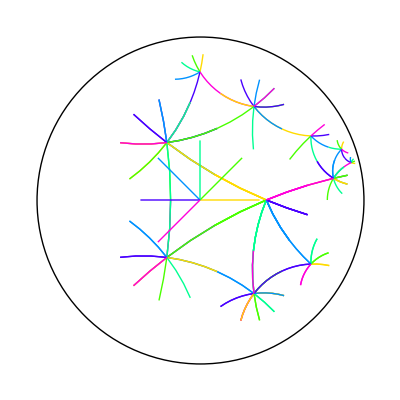

```mathematica
Show[Graphics[Join[{Circle[{0,0},1]},
		BasicDrawMotif/@tiling],AspectRatio->Automatic,PlotRange->All]]
```

### 23x

```mathematica
legLengths["tGp"]=Table[2ArcCosh[Cos[π/3]/Sin[π/7]]//N,{k,1,7}];
vertexAngles["tGp"]=Table[2π/7. k,{k,0,6}];


	

indices["tGp"]={
		{0,1,1,,3},
		{1,1,3,,3},
		{-1,1,1,,3},
		{3,1,1,,3},
		{1,-1,1,,3},
		{-1,-1,1,,3},
		{-3,1,1,,3}
	};

Subscript[ℒ, "tGp"]=Length[indices["tGp"]];
AddTransforms["tGp"];
```

```mathematica
sstart=ReplacePart[MotifRule[Motif["tGp",-1,1,1,Ident]],3,{1,2}];
```

```mathematica
tiling= 
	
	(tXX={Motif["tGp",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
2,
	stopFunction[.01]],tXX]);
```

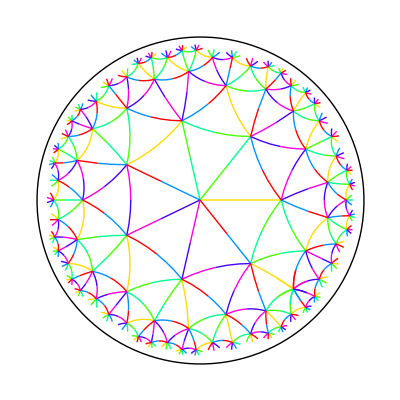

```mathematica
Show[Graphics[Join[{Circle[{0,0},1]},
		BasicDrawMotif/@tiling],AspectRatio->Automatic,PlotRange->All]]
```

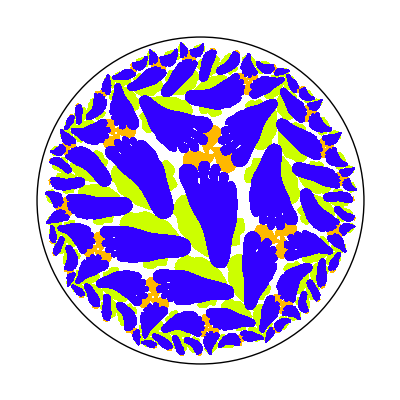

```mathematica
Show[Graphics[Join[{Circle[{0,0},1]},
	
		
			{Hue[.2]},
		DrawMotif[(#∘Mobius[Trans2Point[0,-.2I]]∘Mobius[Rot[.13π]]∘Mobius[Trans2Point[0,-.23I]])&/@
						
						
						(Real2Comp/@ (1.3 rock)),{{},#⟦5⟧}]&
						/@tiling,
			{Hue[.12]},
				DrawMotif[(#∘Mobius[Rot[π .22]]∘Mobius[Trans2Point[0,-.02I]]∘Mobius[{{1.4,0},{0,1}}]∘
				Mobius[Trans[ArcCosh[Cot[π/3]Cot[π/7.]]]]∘Mobius[Rot[3π/7.]]
				
				)&/@
						
						
						(Real2Comp/@ (petal)),{{},#⟦5⟧}]&
						/@tiling,
			
			
			{Hue[.7]},
				DrawMotif[(#∘Mobius[Trans2Point[0,-.2I]]∘Mobius[Rot[.13π]]∘Mobius[Trans2Point[0,-.27I]]∘Mobius[Trans2Point[0,.02]])&/@
						
						
						(Real2Comp/@ (1.3 foot)),{{},#⟦5⟧}]&
						/@tiling
			
			
				
		
		
		
		
		],AspectRatio->Automatic,PlotRange->All]]
```

```mathematica
Show[Graphics[Join[{Circle[{0,0},1]},
	
		
		
		DrawMotifK[(#∘Mobius[{{1.5,0},{0,1}}]∘Mobius[Trans2Point[0,-.2-.2I]])&/@
						
						
						(Real2Comp/@ (1.3 dragonwickR)),{{},#⟦5⟧}]&
						/@tiling
		],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

#### Bulatov's idea

```mathematica
newdraw[motif_,letter_]:=Line[cleanpath[(Comp2Real[logit[#∘letter]]&)/@motif]]

tiling= ReplacePart[#,5->#⟦5⟧∘Mobius[Rot[Pi/7]]]&/@
	
	(tXX={Motif["tGp",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
2,
	stopFunction[.01]],tXX]);
```

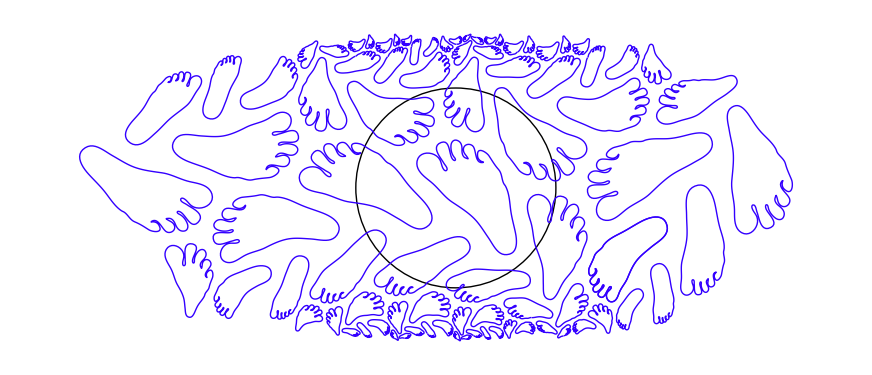

```mathematica
Show[Graphics[Join[{Circle[{0,0},1]},
	
		
	(*		{Hue[.2]},
		newdraw[(#∘Mobius[Trans2Point[0,-.2I]]∘Mobius[Rot[.13π]]∘Mobius[Trans2Point[0,-.23I]])&/@
						(Real2Comp/@ (1.3 rock)),#⟦5⟧]&/@tiling,
			{Hue[.12]},
				newdraw[(#∘Mobius[Rot[π .22]]∘Mobius[Trans2Point[0,-.02I]]∘Mobius[{{1.4,0},{0,1}}]∘
				Mobius[Trans[ArcCosh[Cot[π/3]Cot[π/7.]]]]∘Mobius[Rot[3π/7.]]
				
				)&/@(Real2Comp/@ (petal)),#⟦5⟧]&/@tiling,*)
			
			
			{Hue[.7]},
				newdraw[(#∘Mobius[Trans2Point[0,-.2I]]∘Mobius[Rot[.13π]]∘Mobius[Trans2Point[0,-.27I]]∘Mobius[Trans2Point[0,.02]])&/@(Real2Comp/@ (1.3 foot)),#⟦5⟧]&/@tiling
			
			
				
		
		
		
		
		],AspectRatio->Automatic,PlotRange->All]]
```

### ox, xxx

```mathematica
legLengths["ox"]=legLengths["xxx"]=Table[2ArcCosh[Cos[π/6]/Sin[π/6]]//N,{k,1,7}];
vertexAngles["ox"]=vertexAngles["xxx"]=Table[2π/6. k,{k,0,5}];


	

indices["ox"]={
		{3,-1,1,,3},
		{3,1,1,,3},
		{3,1,1,,3},
		{3,-1,1,,3},
		{3,1,1,,3},
		{3,1,1,,3}
	};

Subscript[ℒ, "ox"]=Length[indices["ox"]];
AddTransforms["ox"];
```

```mathematica
indices["xxx"]={
		{1,-1,1,,3},
		{-1,-1,1,,3},
		{1,-1,1,,3},
		{-1,-1,1,,3},
			{1,-1,1,,3},
		{-1,-1,1,,3}
	};

Subscript[ℒ, "xxx"]=Length[indices["xxx"]];
AddTransforms["xxx"];
```

```mathematica
sstart=ReplacePart[MotifRule[Motif["ox",-1,1,1,Ident]],3,{1,2}];
```

```mathematica
tiling= 
	
	(tXX={Motif["ox",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
4,
	stopFunction[.01]],tXX]);
```

```mathematica
Show[Graphics[Join[{Circle[{0,0},1]},
		BasicDrawMotif/@tiling],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
tiling= 
	
	(tXX={Motif["ox",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
1,
	stopFunction[.03]],tXX]);
```

```mathematica
scootch = Mobius[Trans2Point[.3+.3I,0]]∘Mobius[Rot[-π .03]]∘Mobius[{{1.1,0},{0,1}}]∘Mobius[Rot[π/3]];
ssize=2.15;

Show[Graphics[Join[{Circle[{0,0},1]},
			
		DrawMotif[(#∘scootch)&/@
						(Real2Comp/@ (ssize face1)),{{},#⟦5⟧}]&
						/@tiling
			,
		DrawMotif[(#∘scootch)&/@
						(Real2Comp/@ (ssize face2)),{{},#⟦5⟧}]&
						/@tiling
			
		],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
sstart=ReplacePart[MotifRule[Motif["xxx",-1,1,1,Ident]],3,{1,2}];
```

```mathematica
tiling= 
	
	(tXX={Motif["xxx",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
0,
	stopFunction[.14]],tXX]);
```

```mathematica
scootch = Mobius[Trans2Point[.3+.3I,0]]∘Mobius[Rot[-π .03]]∘Mobius[{{1.1,0},{0,1}}]∘Mobius[Rot[π/3]];
ssize=2.15;

Show[Graphics[Join[{Circle[{0,0},1]},
			
		DrawMotif[(#∘scootch)&/@
						(Real2Comp/@ (ssize face1)),{{},#⟦5⟧}]&
						/@tiling
			,
		DrawMotif[(#∘scootch)&/@
						(Real2Comp/@ (ssize face2)),{{},#⟦5⟧}]&
						/@tiling
			
		],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

### *n *

We have parameters to play with. Choose a value for a, the "width" separating the two kaleidoscopes. Fix n.

-Graphics-

```mathematica
aa=1;
nn=3;

setUpSNS:=(
resetIndices;

indices["*n*"]={
		{0,-1,nn,,2},
		{0,-1,1,,2},
		{2,1,1,,2},
		{0,-1,1,,2},
		{-2,1,1,,2}
	};




bb=ArcCosh[(Cosh[aa]^2+Cos[π/nn])/Sinh[aa]^2];
	hh=ArcCosh[Cosh[aa]   /Sin[π/nn/2]];
(*fix the central point at hh/2 and move around to find the remaining distances*)
mm = 0∘Trans2Point[0,I,hh/3];
hm = 0∘Trans2Point[0,I,hh];
am = 0∘Mobius[Trans2Point[0, I, aa]]∘Mobius[Trans[-bb/2]];
len1 = DiskDistance[mm,mm1=mm∘Trans[-bb]];
len2 = DiskDistance[mm, (*reflect across one of the upper arcs*)
		mm2=mm∘Mobius[Trans2Point[am,0]]∘Mobius[Rot[-Arg[hm∘Trans2Point[am,0]]]]∘Mobius[Refx]∘Mobius[Rot[Arg[hm∘Trans2Point[am,0]]]]∘Mobius[Trans2Point[0,am]]
		];

ang1=2 DiskAngleBetwixt[hm,mm,mm2];
ang2=DiskAngleBetwixt[mm2,mm,mm1];
ang3=DiskAngleBetwixt[mm1,mm,0];

		
	
legLengths["*n*"]={len2, len2,len1,2 hh/3,len1};
vertexAngles["*n*"]={0,ang1,ang1+ang2,ang1+ang2+ang3,ang1+ang2+2 ang3};

Subscript[ℒ, "*n*"]=Length[indices["*n*"]];
AddTransforms["*n*"];
		
	standardStart:=Append[ReplacePart[MotifRule[Motif["*n*",0,1,1,Ident]],3,{1,2}],FanVertexFrom[0,Motif["*n*",0,1,1,Ident]]⟦-1⟧];
	)

setUpSNS;
```

```mathematica
sstart=standardStart;
```

```mathematica
tiling= 
	
	(tXX={Motif["*n*",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
10,
	stopFunction[.01]],tXX]);

(*tiling=Select[tiling, stopFunction[.02][#]&];*)
```

```mathematica
Show[Graphics[Join[{Circle[{0,0},1]},
		BasicDrawMotif/@tiling],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
sstart=standardStart;
tiling= 
	
	(tXX={Motif["*n*",-1,1,1,Trans[.5]]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
1,
	stopFunction[.01]],tXX]);

(*tiling=Select[tiling, stopFunction[.02][#]&];*)
```

```mathematica
ssize=2.4;
scootch=Mobius[Trans2Point[0,-.4 -.4I]]∘Mobius[Rot[-π .3]];
scootch=Mobius[Trans2Point[0,-.4 -.44I]]∘Mobius[Rot[-π .125]];

ssize = 2;
scootch = 	Trans[-1]∘Mobius[{{1.2,0},{0,1}}]∘Trans2Point[0,-.1(1+I)];
themotif = swanBlob;

Show[Graphics[Join[{Circle[{0,0},1],Hue[.12]},
	drawit
			],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
Table[
	aaa=1.1^aaaa;
	aa=aaa;
	nn=3;
setUpSNS;

sstart=standardStart;
tiling= 
	
	(tXX={Motif["*n*",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
10,
	stopFunction[.03]],tXX]);

ssize = 1.4;
scootch = Trans2Point[0,-.1(1+I)];
themotif = swanBlob;
	
	
Show[Graphics[Join[{Circle[{0,0},1]},
		BasicDrawMotif/@tiling
	
	,
				{Circle[{2.5,0},1], Hue[.12]},
	
				DrawMotif[(#∘scootch)&/@
						(Real2Comp/@ (ssize themotif)),{{},#⟦5⟧∘Mobius[{{1,2.5},{0,1}}]}]&
						/@tiling 
			
			],AspectRatio->Automatic,PlotRange->All]]
	,
	
	{aaaa,-15,12}]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

```mathematica
Table[

	aa=1.3;
	nn=nnn;
setUpSNS;

sstart=standardStart;
tiling= 
	
	(tXX={Motif["*n*",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
10,
	stopFunction[.03]],tXX]);

ssize= 1.4;
scootch = Trans2Point[0,-.1(1+I)];
themotif = swanBlob;
	
	
Show[Graphics[Join[{Circle[{0,0},1]},
		BasicDrawMotif/@tiling
	
	,
				{Circle[{2.5,0},1], Hue[.12]},
	
				DrawMotif[(#∘scootch)&/@
						(Real2Comp/@ (ssize themotif)),{{},#⟦5⟧∘Mobius[{{1,2.5},{0,1}}]}]&
						/@tiling 
			
			],AspectRatio->Automatic,PlotRange->All]]
	,
	
	{nnn,2,5}]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

Show[Graphics[Join[{Circle[{0,0},1],
			PointSize[.02]},
			Point[Comp2Real[#]]&/@
			{0,mm,hm,am,0∘Trans[-bb/2]}
			,
		DiskGeodesicArc/@{
			{hm,0},{0,0∘Trans[-bb/2]},{am,0∘Trans[-bb/2]},{am,hm}
				},
		{Hue[.3],PointSize[.03]},
		Point[Comp2Real[#]]&/@{mm2,mm3}
		]
,AspectRatio->Automatic,PlotRange->All]]

## (*2)^p

```mathematica
resetIndices

indices["*22222"]={
		{0,-1,2,,2},
		{0,-1,2,,2},
		{0,-1,2,,2},
		{0,-1,2,,2},
		{0,-1,2,,2}
		}
		;

legLengths["*22222"]=Table[2ArcCosh[Cos[π/4]/Sin[π/5]]//N,{k,1,5}];
vertexAngles["*22222"]=Table[2π/5. k,{k,0,4}];


Subscript[ℒ, "*22222"]=Length[indices["*22222"]];
AddTransforms["*22222"];
		
	standardStart:=Append[ReplacePart[MotifRule[Motif["*22222",0,1,1,Ident]],3,{1,2}],FanVertexFrom[0,Motif["*22222",0,1,1,Ident]]⟦-1⟧];
```

```mathematica
sstart=standardStart;

tiling= 
	
	(tXX={Motif["*22222",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
5,
	stopFunction[.02]],tXX]);

(*tiling=Select[tiling, stopFunction[.02][#]&];*)
```

```mathematica
Show[Graphics[Join[{Circle[{0,0},1]},
		BasicDrawMotif/@tiling],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
Length[tiling]
```

176

```mathematica
sstart=standardStart;

tiling= 
	
	(tXX={Motif["*22222",-1,1,1,Ident]};Join[
		SubIt[{},sstart,
(tXX=Append[tXX,#2];octopusRuleApplication[#1,#2])&,
10,
	stopFunction[.003]],tXX]);

(*tiling=Select[tiling, stopFunction[.02][#]&];*)
```

```mathematica
Length[tiling]
```

156

found with ndimsolve

```mathematica
aa=0.48191;
ll=0.39446;
l2= ArcCosh[Cos[π/5.]/Sin[π/4]];
l3=ArcCosh[(Cos[aa]Cos[2π/3]+Cos[aa])/(Sin[aa]Sin[2π/3])];
```

```mathematica
pp = 0∘Trans2Point[0,I,l2]∘Trans[legLengths["*22222"][[1]]/2];
	p2=pp∘Trans2Point[pp,pp^•, ll];
p3=p2∘Trans2Point[p2,pp^•,l3];
```

```mathematica
ii=0;


Show[Graphics[Join[{Circle[{0,0},1],PointSize[.01],Thickness[.0021]},
			
			
			
			
			
			{Hue[.4], Thickness[.0035]},
			
			DiskGeodesicArc/@
				
				
		(		Join @@ Table[
				{p2∘Mobius[Rot[2π/5 k]]∘#,p2∘Mobius[Rot[2π/5 (k+1)]]∘#}&/@(#[[5]]&/@(tiling))
		,{k,0,4}]
			
			),
			
			{Hue[.2]},
			
				DiskGeodesicArc/@
			
		(		Join @@ Table[
				{pp∘Mobius[Rot[2π/5 k]]∘#,p2∘Mobius[Rot[2π/5 k]]∘#}&/@(#[[5]]&/@(tiling))
		,{k,0,4}]
			
			),
			
		(*	Polygon[Comp2Real/@#]&/@
				
				( {pp∘#,p3∘Mobius[Rot[2π/5]]∘#,0∘#,p3∘#}&/@
					(#[[5]]&/@(tiling)))
					
					
					,
			*)
		
			{GrayLevel[0]},
			
					DiskGeodesicArc/@
			
		(		Join @@ Table[
				{0∘Mobius[Rot[2π/5 k]]∘#,p3∘Mobius[Rot[2π/5 k]]∘#}&/@(#[[5]]&/@(tiling))
		,{k,0,4}]
			
			),
			
			DiskGeodesicArc/@
			
		(		Join @@ Table[
				{pp∘Mobius[Rot[2π/5 k]]∘#,p3∘Mobius[Rot[2π/5 (k+1)]]∘#}&/@(#[[5]]&/@(tiling))
		,{k,0,4}]
			
			),
			
			
			
			
			
		
			{Hue[.42]},
			Point[Comp2Real[#]]&/@
			(Join @@(Outer[#1∘#2&,Join @@(Table[#∘Rot[2π/5 k]
					,{k,0,4}]&/@{pp}),(#[[5]]&/@(tiling)),1])),
			
			
				{GrayLevel[.42]},
			Point[Comp2Real[#]]&/@
			(Join @@(Outer[#1∘#2&,Join @@(Table[#∘Rot[2π/5 k]
					,{k,0,4}]&/@{p2}),(#[[5]]&/@(tiling)),1])),
			
			{GrayLevel[.1]},
			Point[Comp2Real[#]]&/@
			(Join @@(Outer[#1∘#2&,Join @@(Table[#∘Rot[2π/5 k]
					,{k,0,4}]&/@{p3}),(#[[5]]&/@(tiling)),1])),
			
		BasicDrawMotif/@tiling],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
ii=0;


Show[Graphics[Join[{Circle[{0,0},1],PointSize[.01],Thickness[.0021]},
			
		
			Table[Join[{Hue[ii/5]},
			Polygon[Comp2Real[Poinc2Klein[#]]&/@#]&/@
				
				( {pp∘#,p3∘Mobius[Rot[2π/5]]∘#,0∘#,p3∘#}&/@
					((Mobius[Rot[2π /5 ii]]∘#[[5]])&/@(tiling)))],
				{ii,0,4}]
					
					
		(*			,
			
		
			{GrayLevel[0]},
			
					DiskGeodesicArc/@
			
		(		Join @@ Table[
				{0∘Mobius[Rot[2π/5 k]]∘#,p3∘Mobius[Rot[2π/5 k]]∘#}&/@(#[[5]]&/@(tiling))
		,{k,0,4}]
			
			),
			
			DiskGeodesicArc/@
			
		(		Join @@ Table[
				{pp∘Mobius[Rot[2π/5 k]]∘#,p3∘Mobius[Rot[2π/5 (k+1)]]∘#}&/@(#[[5]]&/@(tiling))
		,{k,0,4}]
			
			),
		
			{Hue[.42]},
			Point[Comp2Real[#]]&/@
			(Join @@(Outer[#1∘#2&,Join @@(Table[#∘Rot[2π/5 k]
					,{k,0,4}]&/@{pp}),(#[[5]]&/@(tiling)),1])),
			
			
				{GrayLevel[.42]},
			Point[Comp2Real[#]]&/@
			(Join @@(Outer[#1∘#2&,Join @@(Table[#∘Rot[2π/5 k]
					,{k,0,4}]&/@{p2}),(#[[5]]&/@(tiling)),1])),
			
			{GrayLevel[.1]},
			Point[Comp2Real[#]]&/@
			(Join @@(Outer[#1∘#2&,Join @@(Table[#∘Rot[2π/5 k]
					,{k,0,4}]&/@{p3}),(#[[5]]&/@(tiling)),1])),
			
	*)],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
ii=0;
inset = .1;
corner[1]=p2∘Trans2Point[p2,p3∘Rot[2Pi/5],inset];
corner[2]=p2∘Rot[2Pi/5]∘Trans2Point[p2∘Rot[2Pi/5],p3∘Rot[2Pi/5],inset];
corner[4]=p2∘RotAboutPt[pp,Pi]∘Trans2Point[p2∘RotAboutPt[pp,Pi],p3∘Rot[2Pi/5],inset];
corner[3]=corner[1]∘Trans2Point[corner[1],corner[4], DiskDistance[corner[1],corner[4]]/2];

model = Poinc2Klein;
model = #&;
ShowLines=False;


Show[Graphics[Join[{Circle[{0,0},1],PointSize[.01],Thickness[.0021]},
			
		
			{Hue[.2]},
			
			
 	Table[
			If[model===Poinc2Klein,Polygon[Comp2Real[model[#]]&/@#],(*Polygon[DiskPolygon[#]]*)
					Table[DiskGeodesicArc[{#[[i]],#[[i+1]]}],{i,1,Length[#]-1}]
						
						
						]&/@
				
				( 
						{corner[2]∘#,
							corner[1]∘#,
							corner[3]∘#}
								&/@
					((Mobius[Rot[2π /5 ii]]∘#[[5]])&/@(tiling))),
					
				
				{ii,0,4}],
			
			{Hue[.15]},
			
			
		If[model===Poinc2Klein,Polygon[Comp2Real[model[#]]&/@#],(*Polygon[DiskPolygon[#]]*)Table[DiskGeodesicArc[{#[[i]],#[[i+1]]}],{i,1,Length[#]-1}]]&/@
				
				( 
					Table[p2∘Trans2Point[p2,0,inset]∘Rot[2Pi/5 k]∘#,{k,0,5}]
								&/@
					((#[[5]])&/@(tiling))),
			
			{Hue[0]},
			
If[ShowLines,If[model === Poinc2Klein, 
				Table[
			Line[Comp2Real[model[#]]&/@#]&/@
				
				( 
						{pp∘#,
							pp∘Rot[2Pi/5]∘#}
								&/@
					((Mobius[Rot[2π /5 ii]]∘#[[5]])&/@(tiling))),
				{ii,0,4}],
			
				Join@@
				Table[
			DiskGeodesicArc[{pp∘Rot[2Pi/5 ii]∘#[[5]],pp∘Rot[2Pi/5 (ii+1)]∘#[[5]]}]&/@tiling,{ii,0,4}]
			
			],{}]
				
				
			
			
					
		],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

## archimedean tilings

The idea here is to begin with the permutation code; by hand, construct the octopus. This in turn gives a simple function of l giving the angle sum; we solve this to have angle sum 2pi, which in turn reveals the geometry. We are then home-free.

#### A little set up

```mathematica
MakeArchimedeanVerts[polys_,geometry_,inset_]:=

Module[{angle,vv,cc,angs,ll,pp},
(angle=0;
			angs =Append[ geometry[[2]], geometry[[2,1]]];
			ll=geometry[[1]];
			pp=Append[polys,polys[[1]]];
Table[
		 vv=0∘Trans[ll]∘Rot[angle];
					vv2=0∘Trans[ll]∘Rot[angle+2angs[[i]]];
					aa=ArcSinh[Sinh[ll]/Sin[Pi/pp[[i]]]];
		cc = 0∘Trans[aa]∘Rot[angle+angs[[i]]];
					
					γ=ArcCos[Cosh[ArcSinh[Sinh[ll] Sin[angs[[i]]]/Sin[Pi/pp[[i]]]]-inset] Sin[Pi/pp[[i]]]];
					bb=ArcCosh[Cot[γ]Cot[Pi/pp[[i]]]];
					vv3=0∘Trans2Point[0,cc,aa-bb];
					
			angle =angle+ 2 angs[[i]];
	{vv∘Trans2Point[vv,cc,inset],vv3,vv2∘Trans2Point[vv2,cc,inset],cc}
			
		,{i,1,Length[polys]}])]
```

```mathematica
DrawMotifArchimedean[mot_]:=
	Table[
	{(*Hue[i/7,.2,.3],
					DiskGeodesicArc[{vverts[[i,1]]∘mot[[5]],vverts[[i,2]]∘mot[[5]]}],
			DiskGeodesicArc[{vverts[[i,2]]∘mot[[5]],vverts[[i,3]]∘mot[[5]]}],
		DiskGeodesicArc[{vverts[[i,3]]∘mot[[5]],vverts[[i,4]]∘mot[[5]]}],
		DiskGeodesicArc[{vverts[[i,4]]∘mot[[5]],vverts[[i,1]]∘mot[[5]]}],
		*)
			Hue[i/7,.8,.8],
		DiskGeodesicArc[{vverts[[i,1]]∘mot[[5]],vverts[[i,2]]∘mot[[5]]}],
		DiskGeodesicArc[{vverts[[i,2]]∘mot[[5]],vverts[[i,3]]∘mot[[5]]}]}
		
		
		,{i,1,Length[vverts]}]
```

So, just type in the indices, the depth, the stop size and let her rip!

```mathematica
sameupto= Union[#,
SameTest->(Round[0∘#1[[5]],.001]===Round[0∘#2[[5]],.001]&)]&;
```

```mathematica
MakeArchimedeanPicture[nname_,index_, depth_,stopsize_,inset_,fileout_]:=
	Module[{},
		
		polys=#[[3]] #[[5]]&/@index;
		
		geometry=polys//

({l,ArcSin[Cos[Pi/#]/Cosh[l]]&/@#}/.
(FindRoot[Plus@@( ArcSin[Cos[Pi/#]/Cosh[l]]&/@#) ==Pi,{l,.3}]))&;
vertexAngles["snub"]= 2 geometry[[2]] // Table[Plus@@ Take[#,i],{i,0,Length[#]-1}]& ;
legLengths["snub"] = 2Table[geometry[[1]],{i,Length[geometry[[2]]]}];
resetIndices;
indices["snub"]=index;

Subscript[ℒ, "snub"]=Length[indices["snub"]];
AddTransforms["snub"];

initialMotif= Motif["snub",0,1,1,Ident];
	
	sstart=ReplacePart[MotifRule[initialMotif],3,{1,2}];
tiling= 
(tiles = {initialMotif};
new = tiles;
dcnt = 0;
pnts = Round[0∘#[[5]],.001]&/@new;
While[dcnt < depth && new !={},
dcnt++;
next = Join@@(MotifRule/@new);
new ={};
If[!MemberQ[pnts,p=Round[0∘#[[5]],.001]],
pnts = Append[pnts,p];new = Append[new,#];tiles=Append[tiles,#]]&/@next;
];
sameupto@tiles
);


(*sameupto@(tXX={initialMotif};
		Join[
		SubIt[{},sstart,
(tXX=sameupto@Append[tXX,#2];octopusRuleApplication[#1,#2])&,
depth,
	stopFunction[stopsize],sameupto],tXX]);*)
		
		Print[Length[tiling]];
	
vverts=MakeArchimedeanVerts[polys,geometry,inset];

graphix= Graphics[Join[{Circle[{0,0},1]},(*BasicDrawMotif/@tiling,*)
	DrawMotifArchimedean/@tiling],AspectRatio->Automatic,PlotRange->All];

If[fileout,Export[directory<>nname<>"_"<>(StringJoin@@(ToString/@polys))<>".eps",graphix,"EPS"]];Show[graphix]]
```

```mathematica
MakeArchimedeanPicture[nname_,index_, depth_,stopsize_,inset_,fileout_,sshift_]:=
	Module[{},
		
		polys=#[[3]] #[[5]]&/@index;
		
		geometry=polys//

({l,ArcSin[Cos[Pi/#]/Cosh[l]]&/@#}/.
(FindRoot[Plus@@( ArcSin[Cos[Pi/#]/Cosh[l]]&/@#) ==Pi,{l,.3}]))&;
vertexAngles["snub"]= 2 geometry[[2]] // Table[Plus@@ Take[#,i],{i,0,Length[#]-1}]& ;
legLengths["snub"] = 2Table[geometry[[1]],{i,Length[geometry[[2]]]}];
resetIndices;
indices["snub"]=index;

Subscript[ℒ, "snub"]=Length[indices["snub"]];
AddTransforms["snub"];

initialMotif= Motif["snub",0,1,1,Ident];
	
	sstart=ReplacePart[MotifRule[initialMotif],3,{1,2}];
tiling= sameupto@(tXX={initialMotif};
		sameupto[
		SubIt[{},sstart,
(tXX=sameupto[Append[tXX,#2]];octopusRuleApplication[#1,#2])&,
depth,
	stopFunction[stopsize],sameupto],tXX]);
		
		Print[Length[tiling]];
	
vverts=MakeArchimedeanVerts[polys,geometry,inset];

graphix= Graphics[Join[{Circle[{0,0},1]},(*BasicDrawMotif/@tiling,*)
	DrawMotifArchimedean/@(ReplacePart[#,5->#[[5]] ∘sshift]&/@tiling)],AspectRatio->Automatic,PlotRange->All];

If[fileout,Export[directory<>nname<>"_"<>(StringJoin@@(ToString/@polys))<>".eps",graphix,"EPS"]];Show[graphix]]
```

### And the pictures!

```mathematica
directory="/Users/strauss/Archive/Art/Adobe2GCode/mathematica_output";
directory = "/Users/strauss/Desktop/temp_archs";
directory = "/Users/strauss/Desktop";
directory ="/Users/strauss/Archive/ TheSymmetriesOfThings 2ed II/sot 2 FIGWORK/ch coda";
```

(*
{
#[[1]] is where hooked,
#[[2]] is orientation,
#[[3]] is face center multiplier,
#4[[]] seems not to be used
#5[[]] edge cycle multiplier
} *)

#### some new stuff

913

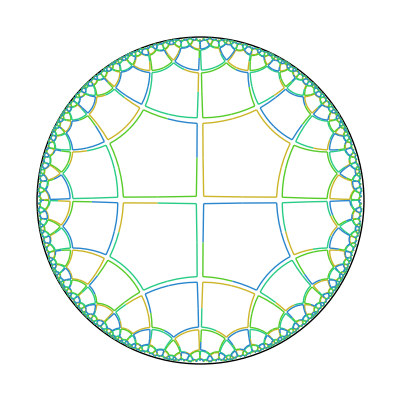

```mathematica
MakeArchimedeanPicture["5444",{

		{0,-1,5,,1},
{0,-1,5,,1},
{0,-1,5,,1},
{0,-1,5,,1}
	},	4,.01,.04,True]
```

1305

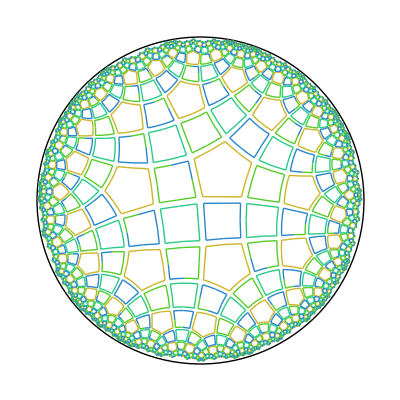

```mathematica
MakeArchimedeanPicture["5444",{

		{0,-1,5,,1},
		{0,-1,4,,1},
		{0,-1,4,,1},
		{0,-1,4,,1}
	},	7,.01,.04,True]
```

```mathematica
MakeArchimedeanPicture["5444",{

		{0,-1,5,,1},
		{0,-1,4,,1},
		{0,-1,4,,1},
		{0,-1,4,,1}
	},	4,.01,.04,True]
```

#### (0)(12)(34)

```mathematica
MakeArchimedeanPicture["0p12p34p",{
		{1,1,5,,1},
		{4,1,1,,3},
		{1,1,6,,1},
		{4,1,1,,3},
			{0,1,1,,3}
	},	6,.01,.04,True]
```

Set::partw: Part 1 of {} does not exist.

5167

-Graphics-

```mathematica
MakeArchimedeanPicture["0p12p34p",{
		{1,1,5,,1},
		{4,1,1,,3},
		{1,1,5,,1},
		{4,1,1,,3},
			{0,1,1,,3}
	},	7,.01,.04,True]
```

Set::partw: Part 1 of {} does not exist.

1009

The error here is that one is back tracking tremendously, due to all those dang triagles:

```mathematica
MakeArchimedeanPicture["0p12p34p",{
		{1,1,3,,1},
		{4,1,1,,3},
		{1,1,7,,1},
		{4,1,1,,3},
			{0,1,1,,3}
	},	12,.05,.04,False]
```

Set::partw: Part 1 of {} does not exist.

General::stop: Further output of Set :: "partw" will be suppressed during this calculation.

3679

```mathematica
MakeArchimedeanPicture["0p12p34p",{
		{1,1,4,,1},
		{4,1,1,,3},
		{1,1,5,,1},
		{4,1,1,,3},
			{0,1,1,,3}
	},	12,.02,.04,False]
```

Set::partw: Part 1 of {} does not exist.

1046

#### (0)[1][2][3][4]

```mathematica
MakeArchimedeanPicture["0p1m2m3m4m",
	{
		{0,  1,1, ,4},
		{0,-1,3,,2},
		{0,-1,2,,2},
		{0,-1,2,,2},
		{0,-1,1,,4}
	},
	8,
	.008,
	.04,True]
```

371

#### (0)[1](2)[3][4]

```mathematica
MakeArchimedeanPicture[   "0p1m2p3m4m",({{0, -1, 2, , 4}, {0, 1, 2, , 4}, {0, -1, 3, , 2}, {0, -1, 1, , 4}, {0, 1, 1, , 4}}),	8,.005,.04,True]
```

338

#### (0)(1)[2][3][4]

```mathematica
MakeArchimedeanPicture["0p1p2m3m4m",   ({{0, 1, 1, , 6}, {0, 1, 1, , 6}, {0, -1, 2, , 2}, {0, -1, 3, , 2}, {0, -1, 1, , 6}}),8,.005,.04,True]
```

341

#### [0][1][2][3][4]

41

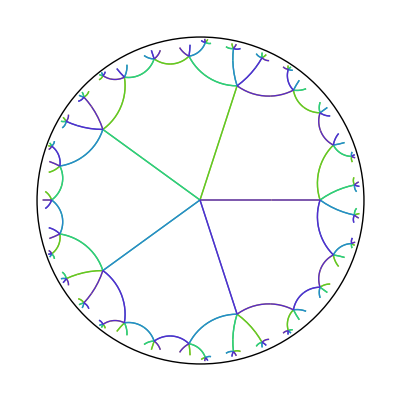

```mathematica
MakeArchimedeanPicture["0m1m2m3m4m",   ({{0, -1, 3, , 2}, {0, -1, 3, , 2}, {0, -1, 3, , 2}, {0, -1, 3, , 2}, {0, -1, 3, , 2}}),3,.03,.00001,True]
```

```mathematica
MakeArchimedeanPicture["0m1m2m3m4m",   ({{0, -1, 2, , 2}, {0, -1, 3, , 2}, {0, -1, 5, , 2}, {0, -1, 4, , 2}, {0, -1, 2, , 2}}),8,.005,.04,True]
```

334

#### (0)(1)[2](34)

```mathematica
MakeArchimedeanPicture["0p1p2m34p",   ({{0, 1, 1, , 8}, {0, 1, 1, , 8}, {0, -1, 1, , 8}, {1, 1, 3, , 1}, {4, 1, 1, , 8}}),8,.005,.04,True]
```

288

#### (0)[1][2](34)

```mathematica
MakeArchimedeanPicture["0p1m2m34p",   ({{0, 1, 1, , 6}, {0, -1, 2, , 2}, {0, -1, 1, , 6}, {1, 1, 3, , 1}, {4, 1, 1, , 6}}),8,.005,.04,True]
```

471

#### (0)[1][2][34]

```mathematica
MakeArchimedeanPicture["0p1m2m34m",   ({{0, 1, 1, , 8}, {0, -1, 2, , 2}, {0, -1, 1, , 8}, {1, -1, 1, , 8}, {4, -1, 1, , 8}}),5,.005,.04,True]
```

275

#### [0][1][2](34)

```mathematica
MakeArchimedeanPicture["0m1m2m34p",   ({{0, -1, 3, , 2}, {0, -1, 2, , 2}, {0, -1, 1, , 4}, {1, 1, 3, , 1}, {4, 1, 1, , 4}}),8,.007,.04,True]
```

541

```mathematica
MakeArchimedeanPicture["0m1m2m34p",   ({{0, -1, 3, , 2}, {0, -1, 4, , 2}, {0, -1, 1, , 4}, {1, 1, 3, , 1}, {4, 1, 1, , 4}}),8,.007,.04,True]
```

373

#### [0][1][2][34]

```mathematica
MakeArchimedeanPicture["0m1m2m34m",   ({{0, -1, 4, , 2}, {0, -1, 2, , 2}, {0, -1, 1, , 6}, {1, -1, 1, , 6}, {4, -1, 1, , 6}}),8,.005,.04,True]
```

299

#### (0)[1](24)(3)

```mathematica
MakeArchimedeanPicture["0p1m24p3p",   ({{0, 1, 1, , 6}, {0, -1, 1, , 6}, {2, 1, 2, , 2}, {0, 1, 2, , 2}, {3, 1, 1, , 6}}),8,.005,.04,True]
```

419

#### (0)[1](24)[3]

```mathematica
MakeArchimedeanPicture["0p1m24p3m",   ({{0, 1, 1, , 6}, {0, -1, 1, , 6}, {2, 1, 1, , 4}, {0, -1, 1, , 4}, {3, 1, 1, , 6}}),8,.005,.04,True]
```

419

#### [0](12)[34]

```mathematica
MakeArchimedeanPicture["0m12p34m",
	{
		{1,1,3,0,1},
		{4,1,1,,8},
		{0,-1,1,,8},
		{1,-1,1,,8},
		{4,-1,1,,8}
	},
	7,.004,.04,True]
```

383

```mathematica
MakeArchimedeanPicture["0m12p34m",
	{
		{1,1,4,0,1},
		{4,1,1,,8},
		{0,-1,1,,8},
		{1,-1,1,,8},
		{4,-1,1,,8}
	},
	1,
	.004,
	.04,True]
```

371

#### (0)(12)[34]

605

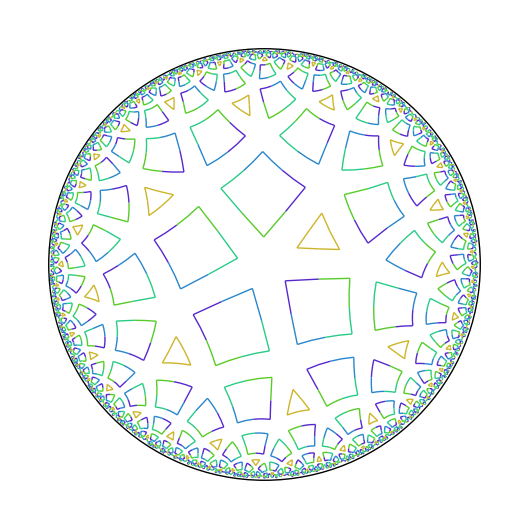

```mathematica
MakeArchimedeanPicture["0p12p34m",
	{
		{1,1,3,0,1},
		{4,1,1,,4},
		{0,1,1,,4},
		{1,-1,1,,4},
		{4,-1,1,,4}
	},
	8,
	.01,
	.15,True]
```

```mathematica
MakeArchimedeanPicture["0p12p34m",
	{
		{1,1,3,0,1},
		{4,1,2,,4},
		{0,1,2,,4},
		{1,-1,2,,4},
		{4,-1,2,,4}
	},
	6,
	.006,
	.04,True]
```

243

#### [0](12)(34)

```mathematica
MakeArchimedeanPicture["0m12p34p",   ({{0, -1, 1, , 6}, {1, 1, 3, , 1}, {4, 1, 1, , 6}, {1, 1, 4, , 1}, {4, 1, 1, , 6}}),8,.005,.04,True]
```

485

```mathematica
MakeArchimedeanPicture["0m12p34p",   ({{0, -1, 1, , 6}, {1, 1, 5, , 1}, {4, 1, 1, , 6}, {1, 1, 4, , 1}, {4, 1, 1, , 6}}),8,.005,.04,True]
```

385

#### (0)(12)[3]

```mathematica
MakeArchimedeanPicture["0p12p3m",   ({{0, 1, 1, , 6}, {1, 1, 3, , 1}, {3, 1, 1, , 6}, {0, -1, 1, , 6}}),8,.005,.04,True]
```

1335

```mathematica
MakeArchimedeanPicture["0p12p3m",   ({{0, 1, 1, , 6}, {1, 1, 4, , 1}, {3, 1, 1, , 6}, {0, -1, 1, , 6}}),8,.005,.04,True]
```

812

```mathematica
MakeArchimedeanPicture["0p12p3m",   ({{0, 1, 1, , 6}, {1, 1, 5, , 1}, {3, 1, 1, , 6}, {0, -1, 1, , 6}}),8,.005,.04,True]
```

636

#### (0)[1][2][3]

```mathematica
MakeArchimedeanPicture["0p1m2m3m",   ({{0, 1, 1, , 4}, {0, -1, 3, , 2}, {0, -1, 2, , 2}, {0, -1, 1, , 4}}),12,.008,.04,True]
```

1482

```mathematica
MakeArchimedeanPicture["0p1m2m3m",   ({{0, 1, 1, , 4}, {0, -1, 3, , 2}, {0, -1, 4, , 2}, {0, -1, 1, , 4}}),12,.008,.04,True]
```

592

#### [0][1][2][3]

```mathematica
MakeArchimedeanPicture["0m1m2m3m",   ({{0, -1, 3, , 2}, {0, -1, 2, , 2}, {0, -1, 2, , 2}, {0, -1, 4, , 2}}),12,.008,.04,True]
```

585

781

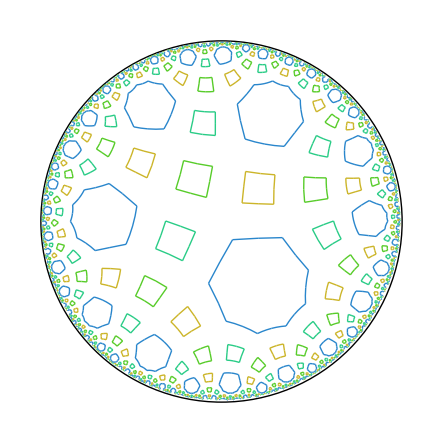

```mathematica
MakeArchimedeanPicture["0m1m2m3m",   ({{0, -1, 2, , 2}, {0, -1, 2, , 2}, {0, -1, 2, , 2}, {0, -1, 4, , 2}}),12,.01,.2,True]
```

419

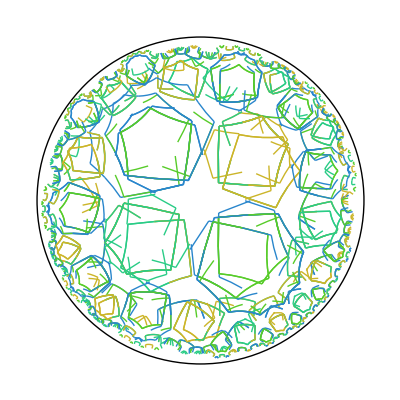

```mathematica
MakeArchimedeanPicture["0m1m2m3m",   ({{0, -1, 5, , 1}, {0, -1, 5, , 1}, {0, -1, 5, , 1}, {0, -1, 4, , 2}}),1,.01,.2,True]
```

#### [0](12)[3]

1016

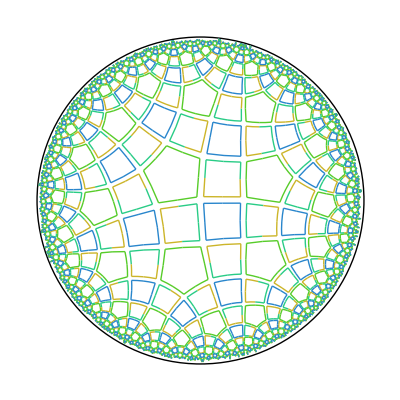

```mathematica
MakeArchimedeanPicture["0m12p3m",   ({{0, -1, 1, , 4}, {1, 1, 5, , 1}, {3, 1, 1, , 4}, {0, -1, 2, , 2}}),8,.02,.04,True]
```

#### (01)(23)

475

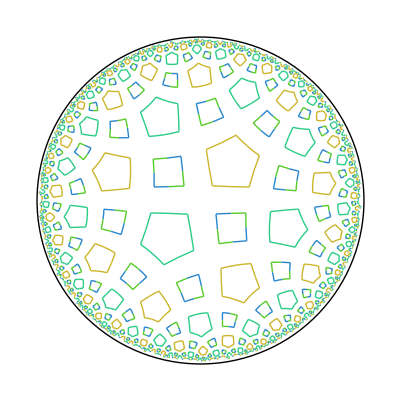

```mathematica
MakeArchimedeanPicture["01p23p",({{1, 1, 5, , 1}, {3, 1, 2, , 2}, {1, 1, 5, , 1}, {3, 1, 2, , 2}}),6,.02,.17,True]
```

shift - to - mate, orientation, order of next face clockwise , name of leg (to look up length), name of corner (to look up angle)

199

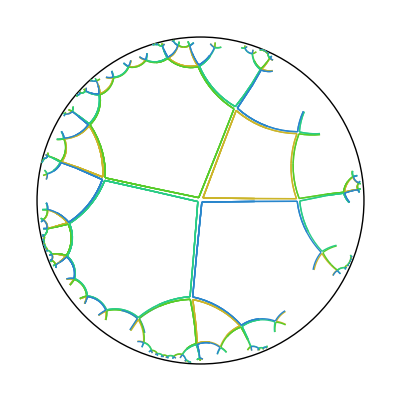

```mathematica
MakeArchimedeanPicture["temp",({{0, -1, 4, , 1}, {0, -1, 5, , 2}, {0, -1, 3, , 3}, {0, -1, 2, , 4}}),2,.1,.02,True]
```

oldstyle

## pq2

This is legacy code, predating the octopus. It uses a direct polygonal subst system.

#### setting things up

```mathematica
stopFunction[tolerance_][letter_]:=(Abs[0∘letter⟦2⟧]<(1-tolerance))
```

```mathematica
complexTilingRuleApplication=Module[{word,rules},
		word=#2;
		rules = #1;

			{#⟦1⟧,#⟦2⟧∘word⟦2⟧}&/@
				
				(Select[rules,#⟦1⟧===word⟦1⟧&][[1,2]])]&
```

Module[{word,rules},word=#2;rules=#1;({#1⟦1⟧,#1⟦2⟧∘word⟦2⟧}&)/@Select[rules,#1⟦1⟧===word⟦1⟧&]⟦1,2⟧]&

```mathematica
OFFSET=.9;
OFFSET=1;
```

```mathematica
DrawTile[p_,q_][letter_]:=Table[
		DiskGeodesicArc[{(OFFSET  verts[p,q]⟦1⟧)∘Rot[2π/p k]∘letter⟦2⟧,(OFFSET  verts[p,q]⟦1⟧)∘Rot[2π/p (k+1)]∘letter⟦2⟧}],
		{k,1,p}]
```

Let's do the {p,q} tiling as a nice test. The motifs will be "rooted" at the origin, with vertices at 2π/p k around

```mathematica
verts[p_,q_]:=verts[p,q]={0∘Trans[ArcCosh[Cot[π/q//N] Cot[π/p//N]]],0∘Trans[ArcCosh[Cos[π/q//N]Csc[π/p//N]]]∘Rot[π/p]}
```

```mathematica
PolyRules[p_,q_]/;(p≥4&&q≥4):=

	
	Join[
{#[[1]],	Join [
			
	Table[
			{Y,Mobius[RotAboutPt[verts[p,q][[1]]∘Rot[2π/p],2π/q j]]∘Mobius[Rot[2π/p*(1+#⟦2⟧)]]
				},
			{j,3,q-2}],
		Join @@ Table[
	Join[
	{{X,Mobius[RotAboutPt[verts[p,q][[2]]∘Rot[2π/p],π]]∘Mobius[Rot[2π/p  k]]}}
						
						,
		Table[
			{Y,Mobius[RotAboutPt[verts[p,q][[1]]∘Rot[2π/p],2π/q j]]∘Mobius[Rot[2π/p  (k+1)]]
				},
			{j,2,q-2}]
						
			],
	{k,1+#⟦2⟧,p-3}],
		
		{{X,Mobius[RotAboutPt[verts[p,q][[2]]∘Rot[2π/p],π]]∘Mobius[Rot[2π/p  (p-2)]]}}

		
		]}&/@
	
{	{X,1},{Y,0}} ,
		
		
{		{S,
				Join @@ Table[
	Join[
	{{X,Mobius[RotAboutPt[verts[p,q][[2]]∘Rot[2π/p],π]]∘Mobius[Rot[2π/p  k]]}}
						
						,
		Table[
			{Y,Mobius[RotAboutPt[verts[p,q][[1]]∘Rot[2π/p],2π/q j]]∘Mobius[Rot[2π/p  (k+1)]]
				},
			{j,2,q-2}]
						
			],
	{k,1,p}]}}
		]//Chop[#,10^-6]&
```

#### making some pictures

```mathematica
tiling= (ss={};Join[
		SubIt[PolyRules[6,7],{{S,Mobius[{{1,0},{0,1}}]}},
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
	13,
	stopFunction[.03]],ss]);
```

```mathematica
Length[tiling]
```

31

Once we have the tiling we can draw anything we please.

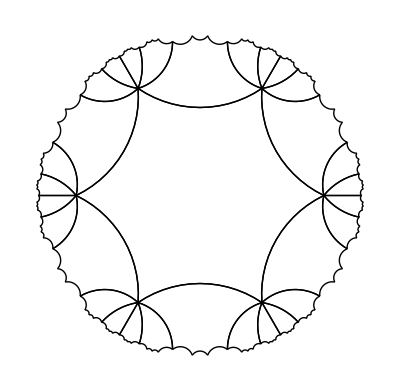

```mathematica
Show[Graphics[Join @@ (DrawTile[6,7]/@tiling),AspectRatio->Automatic,PlotRange->All]]
```

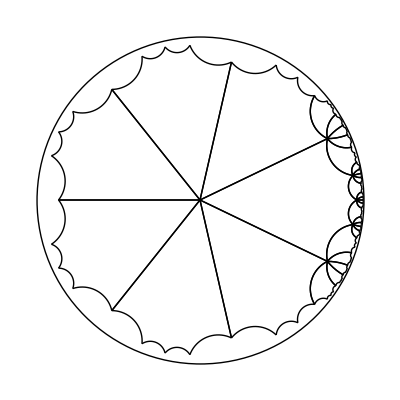

```mathematica
Show[Graphics[{Circle[{0,0},1],

Join @@ (DrawTile[6,7]/@#)},AspectRatio->Automatic,PlotRange->All]]&@({#[[1]],#[[2]]∘Trans[ArcCosh[Cot[π/6.//N] Cot[π/7//N]]]}&/@tiling)
```

```mathematica
DrawTile2[p_,q_][letter_]:=Join @@ Table[
		
		{
		DiskGeodesicArc[{(.95 verts[p,q]⟦1⟧+.1I)∘Rot[2π/p k]∘letter⟦2⟧,(.6 verts[p,q]⟦2⟧)∘Rot[2π/p k]∘letter⟦2⟧}],
				DiskGeodesicArc[{(.6 verts[p,q]⟦2⟧)∘Rot[2π/p k]∘letter⟦2⟧,(.95 verts[p,q]⟦1⟧+.1I)∘Rot[2π/p (k+1)]∘letter⟦2⟧}]
					},
		{k,1,p}]
```

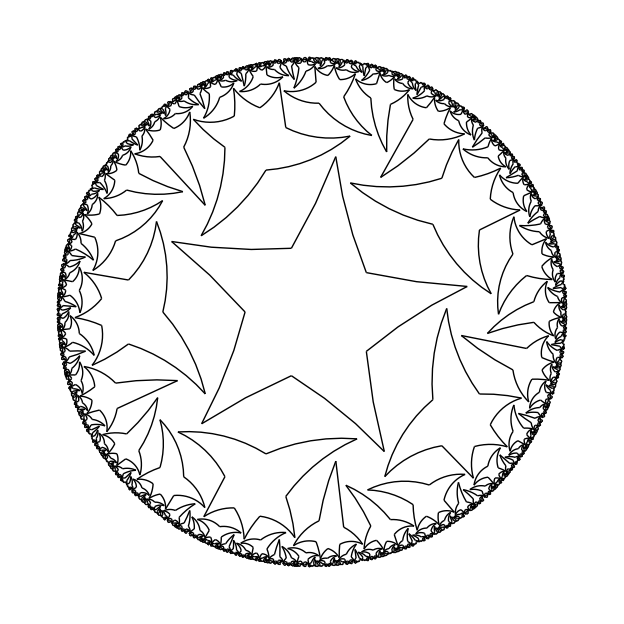

```mathematica
Show[Graphics[Join @@ (DrawTile2[5,6]/@tiling),AspectRatio->Automatic,PlotRange->All]]
```

```mathematica
DrawTile3[p_,q_][t_][letter_]:=Join @@ Table[
		
		{
		DiskGeodesicArc[{(.95 verts[p,q]⟦1⟧+t)∘Rot[2π/p k]∘letter⟦2⟧,(.6 verts[p,q]⟦2⟧)∘Rot[2π/p k]∘letter⟦2⟧}],
				DiskGeodesicArc[{(.6 verts[p,q]⟦2⟧)∘Rot[2π/p k]∘letter⟦2⟧,(.95 verts[p,q]⟦1⟧+t)∘Rot[2π/p (k+1)]∘letter⟦2⟧}]
					},
		{k,1,p}]
```

```mathematica
Table[
	Show[Graphics[Join @@ (DrawTile3[5,6][.1E^(I θ)]/@tiling),AspectRatio->Automatic,PlotRange->All]],{θ,0,2π,π/20}]
```

### Snubs

This works the same way; we only need change the DrawTile command

given pp, qq; of all of this, only useful results are:
 Ll (the length of an edge), La (the distance of the vertex from the origin) and rr (the argument of the vertex).

```mathematica
Clear[vertSn];

vertSn[p_,q_]:=(vertSn[p,q] = (

Cp=Cos[Pi/p] //N; Sp=Sin[Pi/p]//N;Cq=Cos[Pi/q]//N;Sq=Sin[Pi/q]//N;

{Ca,Sa,Cb,Sb}={ca,sa,cb,sb}/.(Solve[{cp  sb/c3 == sa,
	cq     sb/c3 == sa(cb^3-3sb^2 cb)+ca(3sb cb^2-sb^3),
	ca==Sqrt[1-sa^2],
	cb==Sqrt[1-sb^2]}/.{c3->Cos[Pi/3.],cp->Cp,cq->Cq},{sa,sb,ca,cb}])[[2]];
	
Sg=Sa(Cb^3-3Sb^2 Cb)+Ca(3Sb Cb^2-Sb^3);
		Cg=Sqrt[1-Sg^2];
llen[p,q]=Ll=ArcCosh[Cos[Pi/3]/Sb];
La=ArcCosh[Ca/Sa   Cp/Sp];
Lc = ArcCosh[Cg / Sg  Cq/Sq];
Lx = ArcCosh[Cosh[Lc] Cosh[La] - Sinh[Lc] Sinh[La] (-Cb)];
rr=ArcSin[Sb/Sinh[Lx] Sinh[Lc]];
		
		 0∘Trans[La]∘Rot[rr]))
```

```mathematica
Clear[vvT]

vvT[p_,q_][inset_]:=(
		vvT[p,q][inset]={
				vertSn[p,q]∘Trans2Point[vertSn[p,q],0,inset],
				vertSn[p,q]∘Trans2Point[vertSn[p,q],verts[p,q][[1]],inset],
				ccc=vertSn[p,q]∘Trans2Point[vertSn[p,q],vertSn[p,q]∘Rot[2Pi/p],2 Ll - ArcCosh[Cb/Sin[Pi/3]]]∘RotAboutPt[vertSn[p,q]∘Trans2Point[vertSn[p,q],vertSn[p,q]∘Rot[2Pi/p],Ll],-Pi/2];
				vertSn[p,q]∘Trans2Point[vertSn[p,q], ccc, inset],
				vertSn[p,q]∘Rot[2Pi/p]∘Trans2Point[vertSn[p,q]∘Rot[2Pi/p],ccc,inset],
				vertSn[p,q]∘Rot[-2Pi/p]∘RotAboutPt[verts[p,q][[1]],-2Pi/q]∘Trans2Point[vertSn[p,q]∘Rot[-2Pi/p]∘RotAboutPt[verts[p,q][[1]],-2Pi/q],ccc,inset]
			
			
			})
```

```mathematica
DrawTile4[p_,q_][inset_][letter_]:=Join[
		
		{Hue[.9]},
		Table[DiskGeodesicArc[{
					vvT[p,q][inset][[1]]∘Rot[2Pi/p k]∘letter[[2]],
					vvT[p,q][inset][[1]]∘Rot[2Pi/p (k+1)]∘letter[[2]]}],{k,0,p-1}],
	
		{Hue[.3]},
	Table[
			DiskGeodesicArc[{vvT[p,q][inset][[2]]∘Rot[2Pi/p k]∘letter[[2]], vvT[p,q][inset][[2]]∘RotAboutPt[verts[p,q][[1]],2 Pi/q]∘Rot[2Pi/p k]∘letter[[2]]}],
			{k,0,p-1}],
		
		{Hue[.45]},
		
	Join@@ Table[{
					DiskGeodesicArc[{vvT[p,q][inset][[3]]∘Rot[2Pi/p k]∘letter[[2]], vvT[p,q][inset][[4]]∘Rot[2Pi/p k]∘letter[[2]]}],
					
					DiskGeodesicArc[{vvT[p,q][inset][[4]]∘Rot[2Pi/p k]∘letter[[2]],vvT[p,q][inset][[5]]∘Rot[2Pi/p k]∘letter[[2]]}],
					
					DiskGeodesicArc[{vvT[p,q][inset][[5]]∘Rot[2Pi/p k]∘letter[[2]],vvT[p,q][inset][[3]]∘Rot[2Pi/p k]∘letter[[2]]}]
						
			
				
				
				},
			{k,0,p-1}]

	
	
	
	]
```

```mathematica
Show[Graphics[
		Join[
		Join @@ (DrawTile4[5,6][.06]/@tiling),
			
			
			{GrayLevel[0],Circle[{0,0},1]}
			
	
			]
			
			,AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

### More elaborate graphics

```mathematica
scootch=Mobius[Trans2Point[verts[5,6][[2]]*.7,0]];
```

```mathematica
tiling= 
	
	(ss={};Join[
		SubIt[PolyRules[5,6],{{S,scootch}},
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
8,
	stopFunction[.02]],ss])//Chop[#,10^-5]&;
```

```mathematica
Length[tiling]
```

70

```mathematica
flowers=
	{
	.9 #∘Rot[π .08]&/@
	Flower[5,
		Comp2Real[(.9verts[5,6]⟦1⟧)],
		Comp2Real[(.5verts[5,6]⟦2⟧)],
		{0,.7},
		Comp2Real[(.5verts[5,6]⟦2⟧)],30
		],.9 #∘Rot[π .08]&/@
	Flower[5,
		Comp2Real[(.2verts[5,6]⟦1⟧)],
		Comp2Real[(1verts[5,6]⟦2⟧)],
		{0,.2},
	-	Comp2Real[(.5verts[5,6]⟦2⟧)+.2I],6
		],(.3 #)∘Trans2Point[0,verts[5,6]⟦1⟧]&/@
		Flower[6,
		Comp2Real[(.9 verts[6,6]⟦1⟧)],
		Comp2Real[(.5verts[6,6]⟦2⟧)],
		{0,.7},
	Comp2Real[(.5verts[6,6]⟦2⟧)],14
		],Table[E^(I θ),{θ,0.,2π,2.π/20}]};
```

```mathematica
Show[Graphics[ 
		Join[
			{Circle[{0,0},1]},
		
				{RGBColor[.2,.7,.3]},
		(DrawMotif[flowers⟦2⟧,#]&/@tiling),	
			{RGBColor[.6,.5,.2]},
		(DrawMotif[flowers⟦1⟧,#]&/@tiling),
			
				{RGBColor[.8,.2,.3]},
	If[#⟦1⟧===X,
				DrawMotif[(#∘Rot[2π/5 ])&/@flowers⟦3⟧,#]]
							&/@tiling,
			
				{RGBColor[.6,.32,.9]},
	If[#⟦1⟧===X,
				DrawMotif[ ((.03#+verts[5,6][[1]])∘Rot[2π/5])&/@flowers⟦4⟧,#]]
							&/@tiling,
			
			
				{RGBColor[.9,.9,.2]},
		(DrawMotif[.6#∘Rot[ π/5]&/@flowers⟦2⟧,#]&/@tiling),	
			{RGBColor[.8,.75,.2]},
			
					(DrawMotif[.1flowers⟦4⟧,#]&/@tiling)
			
			],
		
		
		
		AspectRatio->Automatic,PlotRange->All]]
```

-Graphics-

#### old

```mathematica
scootch=Mobius[Trans2Point[verts[5,6][[2]]*.7,0]];

tiling= 
	
	(ss={};Join[
		SubIt[PolyRules[5,6],{{S,scootch}},
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
3,
	stopFunction[.04]],ss])//Chop[#,10^-5]&;
```

```mathematica
Show[Graphics[ 
		Join[
			{Circle[{0,0},1]},
		
				{RGBColor[.2,.7,.3]},
		(DrawMotifK[flowers⟦2⟧,#]&/@tiling),	
			{RGBColor[.6,.5,.2]},
		(DrawMotifK[flowers⟦1⟧,#]&/@tiling),
			
				{RGBColor[.8,.2,.3]},
	If[#⟦1⟧===X,
				DrawMotifK[(#∘Rot[2π/5 ])&/@flowers⟦3⟧,#]]
							&/@tiling,
			
				{RGBColor[.6,.32,.9]},
	If[#⟦1⟧===X,
				DrawMotifK[ ((.03#+verts[5,6][[1]])∘Rot[2π/5])&/@flowers⟦4⟧,#]]
							&/@tiling,
			
			
				{RGBColor[.9,.9,.2]},
		(DrawMotifK[.6#∘Rot[ π/5]&/@flowers⟦2⟧,#]&/@tiling),	
			{RGBColor[.8,.75,.2]},
			
					(DrawMotifK[.1flowers⟦4⟧,#]&/@tiling)
			
			],
		
		
		
		AspectRatio->Automatic,PlotRange->All]]
```

Polygon::list: List expected at position 1 in Polygon[Null].

General::stop: Further output of Polygon :: "list" will be suppressed during this calculation.

⁃Graphics⁃

```mathematica
DrawTile[p_,q_][letter_]:=Join @@ Table[
		
		{
		DiskGeodesicArc[{(.95 verts[p,q]⟦1⟧)∘Rot[2π/p k]∘letter⟦2⟧,(.95 verts[p,q]⟦1⟧)∘Rot[2π/p (k+1)]∘letter⟦2⟧}]
					},
		{k,1,p}]
```

```mathematica
Show[Graphics[Join @@ (DrawTile[5,6]/@tiling),AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
DrawTileK[p_,q_][letter_]:=Join @@ Table[
		
		{
		Line[Comp2Real[Poinc2Klein[#]]&/@
					
					
					{(.95 verts[p,q]⟦1⟧)∘Rot[2π/p k]∘letter⟦2⟧,(.95 verts[p,q]⟦1⟧)∘Rot[2π/p (k+1)]∘letter⟦2⟧}]
					},
		{k,1,p}]
```

```mathematica
Show[Graphics[Join @@ (DrawTileK[5,6]/@tiling),AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
scootch=Mobius[Trans2Point[verts[5,6][[2]]*.7,0]]∘Disk2Plane
```

Mobius[{{0.09+0.623874 I,0.09-0.623874 I},{-0.376126-0.09 I,-0.376126+0.09 I}}]

```mathematica
tiling= 
	
	(ss={};Join[
		SubIt[PolyRules[5,6],{{S,scootch}},
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
7,
	Module[{ss=Im[0∘#⟦2⟧],rr=Re[0∘#⟦2⟧]},Abs[rr]<4&&ss>.003&&ss<4]&],ss])//Chop[#,10^-5]&;
```

```mathematica
Show[Graphics[ 
		Join[
			{Line[{{-3,0},{3,0}}]},
		
				{RGBColor[.2,.7,.3]},
		(DrawMotif[flowers⟦2⟧,#]&/@tiling),	
			{RGBColor[.6,.5,.2]},
		(DrawMotif[flowers⟦1⟧,#]&/@tiling),
			
				{RGBColor[.8,.2,.3]},
	If[#⟦1⟧===X,
				DrawMotif[(#∘Rot[2π/5 ])&/@flowers⟦3⟧,#]]
							&/@tiling,
			
				{RGBColor[.6,.32,.9]},
	If[#⟦1⟧===X,
				DrawMotif[ ((.03#+verts[5,6][[1]])∘Rot[2π/5])&/@flowers⟦4⟧,#]]
							&/@tiling,
			
			
				{RGBColor[.9,.9,.2]},
		(DrawMotif[.6#∘Rot[ π/5]&/@flowers⟦2⟧,#]&/@tiling),	
			{RGBColor[.8,.75,.2]},
			
					(DrawMotif[.1flowers⟦4⟧,#]&/@tiling)
			
			],
		
		
		
		AspectRatio->Automatic,PlotRange->2{{-1,1},{0,1}}]]
```

-Graphics-

⁃Graphics⁃

## p∞2, ∞^p 2^p

for fast and dirty, we won't rewrite the octopus code for this task, but will just use a direct substitution.
Also, to save time, we will actually tile by ideal p-gons; the additional symmetry will be in the interior.

#### setting things up

```mathematica
stopFunction[tolerance_][letter_]:=(Abs[0∘letter⟦2⟧]<(1-tolerance))
```

```mathematica
complexTilingRuleApplication=Module[{word,rules},
		word=#2;
		rules = #1;

			{#⟦1⟧,#⟦2⟧∘word⟦2⟧}&/@
				
				(Select[rules,#⟦1⟧===word⟦1⟧&][[1,2]])]&
```

Module[{word,rules},word=#2;rules=#1;({#1⟦1⟧,#1⟦2⟧∘word⟦2⟧}&)/@Select[rules,#1⟦1⟧===word⟦1⟧&]⟦1,2⟧]&

```mathematica
DrawTile[p_,∞][letter_]:=Join @@Table[
		
		{
		DiskGeodesicArc[{(.99 )∘Rot[2π/p k]∘letter⟦2⟧,   (.75 (Sec[π/p]-Tan[π/p])E^(π/p I))∘Rot[2π/p (k )]∘letter⟦2⟧}],
		
				DiskGeodesicArc[{(.99 )∘Rot[2π/p (k+1)]∘letter⟦2⟧,   (.75 (Sec[π/p]-Tan[π/p])E^(π/p I))∘Rot[2π/p (k )]∘letter⟦2⟧}]
					

		
		},
		{k,1,p}]
```

```mathematica
parRotBy[p_]:=(parRotBy[p]=(Mobius[{{1-Q,1-Q},{-1-Q,Q+1}}]∘
Mobius[{{1,2},{0,1}}]∘
Mobius[{{Q+1,Q-1},{Q+1,1-Q}}])/.{Q->E^(2Pi/p I)}//Simplify)
```

```mathematica
PolyRules[p_,∞]:=(*PolyRules[p,∞]= *)

	{
		
		{S,Table[
					{Y,parRotBy[p]∘Rot[2π/p k]},{k,0,p-1}]},
		{Y,Table[
					{Y,parRotBy[p]∘Rot[2π/p k]},{k,0,p-2}]}
		}
```

```mathematica
tiling= 
	
	(ss={};Join[
		SubIt[PolyRules[5,∞],{{S,Mobius[{{1,0},{0,1}}]}},
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
10,
	stopFunction[.005]],ss]);
```

Once we have the tiling we can draw anything we please.

```mathematica
Show[Graphics[Join @@ (DrawTile[5,∞]/@tiling),AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
tiling= 
	
	(ss={};Join[
		SubIt[PolyRules[3,∞],{{S,Mobius[{{1,0},{0,1}}]}},
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
2,
	stopFunction[.005]],ss]);
```

Once we have the tiling we can draw anything we please.

```mathematica
Show[Graphics[Join @@ (DrawTile[3,∞]/@tiling),AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
tiling= 
	
	(ss={};Join[
		SubIt[PolyRules[3,∞],Table[{S,Rot[2Pi/3 k]},{k,0,0}],
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
20,
	stopFunction[.005]],ss]);
```

```mathematica
ssize = {1,1.5} .85;
scootch =Rot[Pi/2-Pi/180  20.5]∘Trans[2.4]∘Mobius[{{1.1,0},{0,1}}]∘
parRotBy[-3];

Show[Graphics[Join[
		{RGBColor@@({216,239,140}/255),
				Disk[{0,0},1],GrayLevel[.5],
			Circle[{0,0},1], Hue[.12]},
	
			Join @@ (Join @@(Join @@
					Table[{
								
								{RGBColor@@ (callaColors[[i]])},
				
							DrawMotif[(#∘scootch∘Rot[2/3 Pi k])&/@
						(Real2Comp/@ (ssize #&/@CallaLily[[i]])),{{},#⟦2⟧}]&
						/@tiling,
							
							{RGBColor@@ (callaOutlineColors[[i]])},
							
							DrawMotif[(#∘scootch∘Rot[2/3 Pi k])&/@
						(Real2Comp/@ (ssize #&/@CallaLily[[i]])),{{},#⟦2⟧},Line]&
						/@tiling
							
							} ,{i,1,5},{k,0,2}]))],AspectRatio->Automatic,PlotRange->All]]
```

Line::list: List expected at position 1 in Line[Null].

General::stop: Further output of Line :: "list" will be suppressed during this calculation.

⁃Graphics⁃

```mathematica
tiling= 
	
	(ss={};Join[
		SubIt[PolyRules[3,∞],Table[{S,Rot[2Pi/3 k]},{k,0,0}],
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
10,
	stopFunction[.003]],ss]);
```

```mathematica
Length[tiling]
```

646

```mathematica
ssize = {1,1.5} .75;
scootch =Rot[Pi/2-Pi/180  1.5]∘Trans[2]∘Mobius[{{1.1,0},{0,1}}]∘
parRotBy[-3];

Show[Graphics[Join[
		{RGBColor@@({216,239,140}/255),
				Disk[{0,0},1],GrayLevel[.5],
			Circle[{0,0},1], Hue[.12]},
	
			Join @@ (Join @@ (Join @@(Join @@
					Table[{
								
								{RGBColor@@ (callaColors[[i]])},
				
							DrawMotif[(#∘scootch∘Rot[2/3 Pi k]∘If[kk==-1,Mobius[Ident]^•, Ident])&/@
						(Real2Comp/@ (ssize #&/@CallaLily[[i]])),{{},#⟦2⟧}]&
						/@tiling,
							
							{RGBColor@@ (callaOutlineColors[[i]])},
							
							DrawMotif[(#∘scootch∘Rot[2/3 Pi k]∘If[kk==-1,Mobius[Ident]^•, Ident])&/@
						(Real2Comp/@ (ssize #&/@CallaLily[[i]])),{{},#⟦2⟧},Line]&
						/@tiling
							
							} ,{i,1,5},{k,0,2},{kk,-1,1,2}])))],AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
ssize = {1,1.5} .75;
scootch =Rot[Pi/2-Pi/180  1.35]∘Trans[2]∘Mobius[{{1.1,0},{0,1}}]∘
parRotBy[-3];

Show[Graphics[Join[
		{RGBColor@@({216,239,140}/255),
				Polygon[{{-2,0},{2,0},{2,2},{-2,2}}],GrayLevel[.5],
			Line[{{-2,0},{2,0}}], Hue[.12]},
	
			Join @@ (Join @@ (Join @@(Join @@
					Table[{
								
								{RGBColor@@ (callaColors[[i]])},
				
							DrawMotif[(#∘scootch∘Rot[2/3 Pi k]∘If[kk==-1,Mobius[Ident]^•, Ident])&/@
						(Real2Comp/@ (ssize #&/@CallaLily[[i]])),{{},#⟦2⟧∘Rot[Pi]∘Disk2Plane}]&
						/@tiling,
							
							{RGBColor@@ (callaOutlineColors[[i]])},
							
							DrawMotif[(#∘scootch∘Rot[2/3 Pi k]∘If[kk==-1,Mobius[Ident]^•, Ident])&/@
						(Real2Comp/@ (ssize #&/@CallaLily[[i]])),{{},#⟦2⟧∘Rot[Pi]∘Disk2Plane},Line]&
						/@tiling
							
							} ,{i,1,5},{k,0,2},{kk,-1,1,2}])))],AspectRatio->Automatic,PlotRange->{{-2,2},{-.01,2}}]]
```

Line::list: List expected at position 1 in Line[Null].

General::stop: Further output of Line :: "list" will be suppressed during this calculation.

⁃Graphics⁃

Further examples

## An Aperiodic Archimedean Example

We'll do this by hand for now: this is a 3555; see the paper Reg Prods for details

```mathematica
Protect[{U,l,r,L,R,v}];
```

These are the vertex angles of the pentagon and triangle, respectively.

```mathematica
Unprotect[a,b,α,β,λ,A,B];
α=2ArcCos[1/2 √(1/2 (1+√5)//N)] (*from previous work*);
β=2π-3α ;

λ=ArcCosh[(Cos[β]+Cos[β]^2)/Sin[β]^2];

a= ArcSinh[Sin[α/2] Sinh[λ]/Sin[2π/5]];
A = ArcSinh[Sin[α/2] Sinh[λ/2]/Sin[π/5]];

b= ArcSinh[Sin[β/2]Sinh[λ]/Sin[2π/3]];
B = ArcSinh[Sin[β/2]Sinh[λ/2]/Sin[π/3]];

pentagonV = Table[0∘Trans[a]∘Rot[2π k/5],{k,0,5}];
triangleV = Table[0∘Trans[b]∘Rot[2π k/3],{k,0,3}];

Protect[α,β,λ,a,b,A,B];
```

```mathematica
rrules={
		{v,{
				{U,Trans[-a]∘Rot[π]∘Trans[b]}
				}},
		{U,{
				{L,RotAboutPt[0∘Trans[a]∘Rot[6π/5],-2α]},
				{v, Trans[B]∘Rot[π]∘Trans[-A]},
				{R,RotAboutPt[0∘Trans[a]∘Rot[4π/5],2α]}
				}},
		{r,{
				{r,Rot[6π/5]∘	RotAboutPt[0∘Trans[a]∘Rot[6π/5],-2α]},
				{v, Trans[B]∘Rot[π]∘Trans[-A]},
				{l,Rot[4π/5]∘	RotAboutPt[0∘Trans[a]∘Rot[4π/5],2α]}
				}},
		{l,{
				{r,Rot[6π/5]∘	RotAboutPt[0∘Trans[a]∘Rot[6π/5],-2α]},
				{v, Trans[B]∘Rot[π]∘Trans[-A]},
				{l,Rot[4π/5]∘	RotAboutPt[0∘Trans[a]∘Rot[4π/5],2α]}
				}},
		{R,{
				{r,Rot[6π/5]∘	RotAboutPt[0∘Trans[a]∘Rot[6π/5],-2α]∘Rot[4π/5]},
				{v, Trans[B]∘Rot[π]∘Trans[-A]∘Rot[4π/5]},
				{R,RotAboutPt[0∘Trans[a]∘Rot[4π/5],2α]∘Rot[4π/5]}
				}},
		{L, {
				{L,RotAboutPt[0∘Trans[a]∘Rot[6π/5],-2α]∘Rot[-4π/5]},
				{v, Trans[B]∘Rot[π]∘Trans[-A]∘Rot[-4π/5]},
				{l,Rot[4π/5]∘	RotAboutPt[0∘Trans[a]∘Rot[4π/5],2α]∘Rot[-4π/5]}
				}}
		
		
		
		}//Chop[#,10^-4]&;
```

,
		
		{Δ,Join @@ Table[{
					{LR,Trans[A]∘Rot[π]∘Trans[-B]∘Rot[2π k/3]},
					{l,Trans[-a]∘Rot[π]∘Trans[b]∘Rot[2π(k+1)/3]}
					},{k,0,2}]
			
			},
		
		{LR, {
				{L,RotAboutPt[0∘Trans[a]∘Rot[6π/5],-2α]∘Rot[-4π/5]},
				{v, Trans[B]∘Rot[π]∘Trans[-A]∘Rot[-4π/5]},
				{l,Rot[4π/5]∘	RotAboutPt[0∘Trans[a]∘Rot[4π/5],2α]∘Rot[-4π/5]},
					{v, Trans[B]∘Rot[π]∘Trans[-A]∘Rot[4π/5]},
				{R,RotAboutPt[0∘Trans[a]∘Rot[4π/5],2α]∘Rot[4π/5]}
				}}

```mathematica
complexTilingRuleApplication=Module[{word,rules},
		word=#2;
		rules = #1;

			{#⟦1⟧,#⟦2⟧∘word⟦2⟧}&/@
				
				(Select[rules,#⟦1⟧===word⟦1⟧&][[1,2]])]&
```

Module[{word,rules},word=#2;rules=#1;({#1⟦1⟧,#1⟦2⟧∘word⟦2⟧}&)/@Select[rules,#1⟦1⟧===word⟦1⟧&]⟦1,2⟧]&

```mathematica
ttriangle=1 ( Join @@ Table[
		
		triangleV⟦1⟧∘(Trans2Point[triangleV⟦1⟧,triangleV⟦2⟧,λ/10*nn ]∘Rot[2π k /3]),{k,0,2},{nn,0,9}])//Append[#,#⟦1⟧]& ;

ppentagon = 1(Join @@ Table[
	pentagonV⟦1⟧∘Trans2Point[pentagonV⟦1⟧,pentagonV⟦2⟧,λ/10*nn ]∘Rot[2π k /5],{k,0,4},{nn,0,9}])//Append[#,#⟦1⟧]&;
```

```mathematica
ttiling=
	
	(ss={};
	Join[
			
	SubIt[
rrules,
	{{r,Rot[π]∘Disk2Plane}},
	
	
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
	
10,Module[{ss=Im[0∘#⟦2⟧],rr=Re[0∘#⟦2⟧]},Abs[rr]<1&&ss>.003&&ss<2]&
			],ss]);
```

Part::partd: Part specification rrules⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Join::heads: Heads complexTilingRuleApplication and List at positions 1 and 2 are expected to be the same.

```mathematica
Show[Graphics[Join[
			{Line[{{-1,0},{1,0},{1,1},{-1,1},{-1,0}}]},
			
			
			Join @@(
			
			(If[#⟦1⟧===v,{Hue[.4],DrawMotif[ttriangle,#]},
					{Hue[.12],DrawMotif[ppentagon,#]}])&/@
				ttiling)],AspectRatio->Automatic,PlotRange->All]]
```

Part::partd: Part specification ppentagon⟦1⟧ is longer than depth of object.

Join::heads: Heads Hue and Polygon at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and Hue at positions 1 and 2 are expected to be the same.

-Graphics-

## 84,53

The geometry can be interpreted in various ways. Here we apply the 54 version:

```mathematica
a=ArcCosh[Cot[Pi/4]Cot[Pi/5]];
b=ArcCosh[Cos[Pi/4]Csc[Pi/5]];

pentagonV=Table[0∘Trans[a]∘Rot[2π/5 k],{k,0,5}];
```

```mathematica
pM=0∘Trans[b]∘Rot[-π/5];
```

```mathematica
rrules={
		{M,{
				{R,RotAboutPt[pentagonV⟦2⟧,π]∘Rot[-4π/5]},
				{L,RotAboutPt[pentagonV⟦1⟧,π]∘Rot[6π/5]},
				{M,RotAboutPt[pentagonV⟦1⟧,π]∘Rot[4π/5]}
	
				}},
		{L,{
				{R,RotAboutPt[pentagonV⟦2⟧,π]∘Rot[-4π/5]},
				{L,RotAboutPt[pentagonV⟦1⟧,π]∘Rot[6π/5]},
				{L,RotAboutPt[pentagonV⟦1⟧,π]∘Rot[4π/5]},
				{M,RotAboutPt[pentagonV⟦1⟧,π]∘Rot[2π/5]}
				
				}},
		
		{R,{
				{R,RotAboutPt[pM^•,π]∘Rot[2π/5]∘RotAboutPt[pM,π]},
				{R,RotAboutPt[pentagonV⟦2⟧,π]∘Rot[-4π/5]},
				{L,RotAboutPt[pentagonV⟦1⟧,π]∘Rot[6π/5]},
				{M,RotAboutPt[pentagonV⟦1⟧,π]∘Rot[4π/5]}
				
				}}
		
		
		
		
		
		
		
		}//Chop[#,10^-4]&;
```

```mathematica
DrawPentagon[{let_,pos_}]:=
	

	Join[
		

{Hue[.1], DiskGeodesicArc[{pentagonV⟦1⟧∘pos,pentagonV⟦5⟧∘pos}]},
	
	(*
	{GrayLevel[0]},
		
		Table[DiskGeodesicArc[{ pentagonV⟦k⟧∘Mobius[{{.9,0},{0,1}}]∘pos,pentagonV⟦1+k⟧∘Mobius[{{.9,0},{0,1}}]∘pos}],{k,1,4}],
		Table[DiskGeodesicArc[{pentagonV⟦k⟧∘Mobius[{{.9,0},{0,1}}]∘RotAboutPt[pM,π]∘pos,pentagonV⟦1+k⟧∘Mobius[{{.9,0},{0,1}}]∘RotAboutPt[pM,π]∘pos}],{k,1,4}],
		
		*)
		{Hue[.8]},
		
		Table[DiskGeodesicArc[{ pentagonV⟦k⟧∘Mobius[{{1,0},{0,1}}]∘pos,pentagonV⟦1+k⟧∘Mobius[{{1,0},{0,1}}]∘pos}],{k,If[let===L,1,2],4}],
		Table[DiskGeodesicArc[{pentagonV⟦k⟧∘Mobius[{{1,0},{0,1}}]∘RotAboutPt[pM,π]∘pos,pentagonV⟦1+k⟧∘Mobius[{{1,0},{0,1}}]∘RotAboutPt[pM,π]∘pos}],{k,1,If[let===R,3,2]}]
		
		
	]
```

```mathematica
DrawPentagonUp[{let_,pos_}]:=	Join[
{Hue[.1], UpPlaneGeodesicArc[{pentagonV⟦1⟧∘pos,pentagonV⟦5⟧∘pos}]},
	
		{Hue[.8]},
		
		Table[UpPlaneGeodesicArc[{ pentagonV⟦k⟧∘Mobius[{{1,0},{0,1}}]∘pos,pentagonV⟦1+k⟧∘Mobius[{{1,0},{0,1}}]∘pos}],{k,If[let===L,1,2],4}],
		Table[UpPlaneGeodesicArc[{pentagonV⟦k⟧∘Mobius[{{1,0},{0,1}}]∘RotAboutPt[pM,π]∘pos,pentagonV⟦1+k⟧∘Mobius[{{1,0},{0,1}}]∘RotAboutPt[pM,π]∘pos}],{k,1,If[let===R,3,2]}]
		]
```

```mathematica
complexTilingRuleApplication=Module[{word,rules},
		word=#2;
		rules = #1;

			{#⟦1⟧,#⟦2⟧∘word⟦2⟧}&/@
				
				(Select[rules,#⟦1⟧===word⟦1⟧&][[1,2]])]&
```

Module[{word,rules},word=#2;rules=#1;({#1⟦1⟧,#1⟦2⟧∘word⟦2⟧}&)/@Select[rules,#1⟦1⟧===word⟦1⟧&]⟦1,2⟧]&

```mathematica
ttiling=
	
	(ss={};
	Join[
			
	SubIt[
rrules,
	{{R,Trans2Point[pM,0.01]∘Rot[.72π]
					}}
					,
	
	
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
	
2,stopFunction[.002]
			],ss]);
```

CompiledFunction::cfsa: Argument (0.425779+0.904827 ⅈ) (-1+0.01 Conjugate[pM]) at position 2 should be a machine-size complex number.

```mathematica
Show[Graphics[DrawPentagon/@ttiling,AspectRatio->Automatic]]
```

⁃Graphics⁃

```mathematica
ttiling=
	
	(ss={};
	Join[
			
	SubIt[
rrules,
	{{R,Trans2Point[pM,0.01]∘Rot[.6π]}}
					,
	
	
(ss=Append[ss,#2];complexTilingRuleApplication[#1,#2])&,
	
6,Module[{ss=Im[0∘#⟦2⟧∘Disk2Plane],rr=Re[0∘#⟦2⟧∘Disk2Plane]},Abs[rr]<2&&ss>.003&&ss<2]&
			],ss]);
```

CompiledFunction::cfsa: Argument (0.404508-0.293893 ⅈ) (-1+0.01 Conjugate[pM])+(0.404508+0.293893 ⅈ) (-0.01+Conjugate[pM]) at position 2 should be a machine-size complex number.

```mathematica
Show[Graphics[DrawPentagonUp/@ttiling,AspectRatio->Automatic,PlotRange->{{-1,1},{0,1}}]]
```

⁃Graphics⁃

drawing some tilings in p*q

A p*q is the same as a division of a regular *q^p into pths. So, to draw a 3*7:

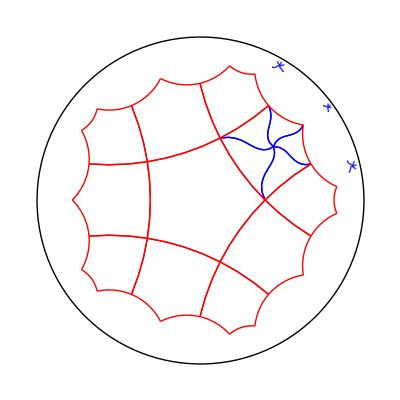

```mathematica
PP=5;QQ=4 ; (*change at will; Q must be even*)
longdiagonal=ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]];
shortdiagonal=ArcCosh[Cos[Pi/QQ]/Sin[Pi/PP]];
halfedge=ArcCosh[Cos[Pi/PP]/Sin[Pi/QQ]];
gon = Table[
0∘Trans[1 ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘Rot[2k Pi/PP],
{k,1,PP+1}];

ashift=0∘Trans[longdiagonal]∘Rot[2Pi/PP]∘Trans[2shortdiagonal]∘Rot[-Pi/PP];

sspline = spline[0,0∘Trans[longdiagonal],.5∘Rot[-Pi/PP],.3 E^(2Pi/PP I)-.6];
sss = Table[sspline/.{t->tt},{tt,0,1,.1}];

rots5 = Table[Rot[2Pi/PP k],{k,1,5}];

ssss = movestuff[sss,rots5];

backref =Mobius[ Trans[shortdiagonal]]∘Mobius[Refy]∘Mobius[Trans[-shortdiagonal]];

group = Join[{Ident},Join@@Outer[#1∘#2&,{Mobius[backref]},(Mobius/@rots5)],
Join@@Outer[#1∘#2&,{RotAboutPt[0∘Trans[longdiagonal],Pi]},(Mobius/@rots5)]];


gg =
Join@@Outer[inverse[#2]∘#1∘#2&,group[[{3,4,7,11,10}]],{Mobius[Trans[2shortdiagonal]]∘Mobius[Rot[Pi/5]]}];


Graphics[{Circle[{0,0},1],
Blue,
Table[
DiskGeodesicArc[{#[[i]],#[[i+1]]}],{i,Length[#]-1}]&/@
movestuffs[Join[ssss],Join[gg]
],
Red,
Table[
DiskGeodesicArc[{#[[i]],#[[i+1]]}],{i,Length[#]-1}]&/@
movestuffs[Join[{gon}],group
]


}]
```